```mathematica
ClearAll["Global`*"]
Quit
```

```mathematica
m=5;
```

Create a m x m central difference matrix

```mathematica
A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;
A //MatrixForm
(* ν = a k/h *)
```

(0 | 1/2 | 0 | 0 | -1/2
-1/2 | 0 | 1/2 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0
0 | 0 | -1/2 | 0 | 1/2
1/2 | 0 | 0 | -1/2 | 0)

Check if there exists a value ν =  a k/h > 0 such that entries of (I - (νA))^-1 are positive. 
The following checks if each off-diagonal entries of  (I - (νA))^-1 can be positive for certain values of ν.
If False is returned, then that means that there is at least a negative off-diagonal entry in  (I + (νA))^-1 for any ν>0

```mathematica
BE = Inverse[IdentityMatrix[Length[A]]-ν A];
listall = Table[Reduce[{BE[[i,j]]≥ 0,ν≠0},ν,Reals],{i,1,m},{j,1,m}];
listoffdiag = Table[If[i≠ j,Reduce[{BE[[i,j]]≥ 0,ν>0},ν,Reals]],{i,1,m},{j,1,m}];
Reduce[DeleteDuplicates[Join@@listall]]//N
DeleteCases[DeleteDuplicates[Join@@listoffdiag],Null]//N
```

ν≤-4.41114||ν≥4.41114

{ν>0.,ν≥4.41114}

```mathematica
BE//MatrixForm
```

((1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16)
(-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16)
(ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16)
(ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16)
(ν/2+ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4-ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (ν^2/4+ν^3/8+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (-ν/2-ν^3/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16) | (1+(3 ν^2)/4+ν^4/16)/(1+(5 ν^2)/4+(5 ν^4)/16))

```mathematica
ν=Root[-8-6 #1^2+#1^3&,1]
DeleteDuplicates[Join@@Table[BE[[i,j]],{i,1,m},{j,1,m}]]//Simplify//N
```

Root[-8-6 #1^2+#1^3&,1]

{0.177815,0.212994,0.109191,0.177815,0.0519017,0.161093,0.,0.161093,-0.0519017}

```mathematica
BE = Inverse[IdentityMatrix[Length[A]]-ν A];
listall = Table[Reduce[{BE[[i,j]]≥ 0, ν ≠0},ν,Reals],{i,1,m},{j,1,m}];
listoffdiag = Table[If[i≠ j,Reduce[{BE[[i,j]]≥ 0,ν ≠0},ν,Reals]],{i,1,m},{j,1,m}];
DeleteCases[DeleteDuplicates[Join@@listall],Null]
DeleteCases[DeleteDuplicates[Join@@listoffdiag],Null]//N
```

{ν<0||ν>0,ν≤Root[128+192 #1^2+80 #1^4+8 #1^6+#1^7&,1]||ν>0,ν≤Root[8+6 #1^2+#1^3&,1]||ν>0,ν<0||ν≥Root[-8-6 #1^2+#1^3&,1],ν<0||ν≥Root[-128-192 #1^2-80 #1^4-8 #1^6+#1^7&,1]}

{ν≤-9.01393||ν>0.,ν<0.||ν>0.,ν≤-6.20761||ν>0.,ν<0.||ν≥6.20761,ν<0.||ν≥9.01393}

Non-repeated off-diagonal entries of (I - (νA))^-1:

```mathematica
DeleteCases[DeleteDuplicates[Join@@Table[If[i≠ j,BE[[i,j]]],{i,1,m},{j,1,m}]],Null]//Simplify
```

{(ν (128+192 ν^2+80 ν^4+8 ν^6+ν^7))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^2 (64+80 ν^2+24 ν^4-2 ν^5+ν^6))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^3 (32+32 ν^2+4 ν^3+6 ν^4+ν^5))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^4 (16-8 ν+12 ν^2-4 ν^3+ν^4))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^4 (16+8 ν+12 ν^2+4 ν^3+ν^4))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^3 (-32-32 ν^2+4 ν^3-6 ν^4+ν^5))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν^2 (64+80 ν^2+24 ν^4+2 ν^5+ν^6))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8),(ν (-128-192 ν^2-80 ν^4-8 ν^6+ν^7))/(256+576 ν^2+432 ν^4+120 ν^6+9 ν^8)}

One can see that if m is even, then there exists a negative entry in (I + (νA))^-1 for ν > 0.
But if m is odd, then we can obtain a lower bound on ν such that all off-diagonal entries are positive. If some matrix entries have numerators that attain negative values, then admissible values of ν for positivity depend on roots of the numerator.

```mathematica
ν=Root[128+192 #1^2+80 #1^4+8 #1^6+#1^7&,1]
DeleteCases[DeleteDuplicates[Join@@Table[BE[[i,j]],{i,1,m},{j,1,m}]],Null]//Simplify//N
```

Root[128+192 #1^2+80 #1^4+8 #1^6+#1^7&,1]

{0.145067,0.,0.145067,0.0321872,0.152208,0.065959,0.166843,0.102978,0.189692}

Check the same in the case of explicit Euler, i.e positivity of I-νA. Obviously this is not true for any value of m.

```mathematica
FE = IdentityMatrix[Length[A]]+ν A;
listall = Table[Reduce[{FE[[i,j]]≥ 0,ν>0},ν,Reals],{i,1,m},{j,1,m}];
listoffdiag = Table[If[i≠ j,Reduce[{FE[[i,j]]≥ 0,ν>0},ν,Reals]],{i,1,m},{j,1,m}];
DeleteCases[DeleteDuplicates[Join@@listall],Null]
DeleteCases[DeleteDuplicates[Join@@listoffdiag],Null]//Simplify
```

{ν>0,False}

{ν>0,False}

```mathematica
FE//MatrixForm
```

(1 | ν/2 | 0 | 0 | -ν/2
-ν/2 | 1 | ν/2 | 0 | 0
0 | -ν/2 | 1 | ν/2 | 0
0 | 0 | -ν/2 | 1 | ν/2
ν/2 | 0 | 0 | -ν/2 | 1)

```mathematica
ClearAll["Global`*"]
Quit
```

```mathematica
m=5;
S =Table[DiagonalMatrix[ConstantArray[(-1)^(j-i+1)/2Cot[(j-1)/2 h],m-1],-1,m],{j,1,m},{i,1,m}]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];
A[[1,m]] = -1/2;
A[[m,1]] = 1/2;
A //MatrixForm
```

DiagonalMatrix::inf: Input matrix contains an infinite entry.

General::stop: Further output of DiagonalMatrix::inf will be suppressed during this calculation.

(0 | 1/2 | 0 | 0 | -1/2
-1/2 | 0 | 1/2 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0
0 | 0 | -1/2 | 0 | 1/2
1/2 | 0 | 0 | -1/2 | 0)

```mathematica
m=5;h =1/(m-1);
Table[ConstantArray[(-1)^(k-1)/2Cot[k/2 h],m-k],{k,1,m}]
```

{{1/2 Cot[1/8],1/2 Cot[1/8],1/2 Cot[1/8],1/2 Cot[1/8]},{-1/2 Cot[1/4],-1/2 Cot[1/4],-1/2 Cot[1/4]},{1/2 Cot[3/8],1/2 Cot[3/8]},{-1/2 Cot[1/2]},{}}

```mathematica
m=5;k=2;ConstantArray[(-1)^(k-1)/2Cot[k/2 h],m-k]
```

{-Cot[h]/2,-Cot[h]/2,-Cot[h]/2}

# Notation: ν vs. ν/2??? Or ν vs. (-ν), so M_(1,2)<0 vs. M_(2,1)<0?

### General θ-methods

```mathematica
m=5;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@A
```

(0 | 1/2 | 0 | 0 | -1/2
-1/2 | 0 | 1/2 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0
0 | 0 | -1/2 | 0 | 1/2
1/2 | 0 | 0 | -1/2 | 0)

```mathematica
Manipulate[Simplify@MatrixForm[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{θ,0,1,1/20}]
```

IdentityMatrix::dims: Dimension specification 0 should be a positive machine integer or a pair of positive machine integers.

### Size=5. For θ=0:

```mathematica
Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]/.θ->0]
```

{0,1,-ν/2,ν/2}

```mathematica
Reduce[(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]/.θ->0]≥0]]
```

ν==0

### Size=5. For θ=1:

```mathematica
Reduce[(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]/.θ->1]≥0]]
```

```mathematica
ν==0||ν≥Root[-8-4 #1^2+#1^3&,1]//N
```

ν==0.||ν≥4.41114

### Size=5. For θ=1/2:

```mathematica
Reduce[(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]/.θ->1/2]≥0]]
```

ν==0

### For 0≤θ≤1:

```mathematica
m=7;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@A
```

(0 | 1/2 | 0 | 0 | 0 | 0 | -1/2
-1/2 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 1/2
1/2 | 0 | 0 | 0 | 0 | -1/2 | 0)

```mathematica
Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]//LogicalExpand
```

(θ==1&&Root[-32-32 #1^2-6 #1^4+#1^5&,1]==ν)||(ν==0&&0≤θ&&θ≤1)||(ν>Root[-64+64 #1+12 #1^2-13 #1^3-7 #1^4+#1^5&,1]&&θ≤1&&Root[64-32 ν^2 #1+112 ν^2 #1^2-32 ν^4 #1^3+56 ν^4 #1^4-6 ν^6 #1^5+7 ν^6 #1^6&,2]≤θ)||(Root[-32-32 #1^2-6 #1^4+#1^5&,1]<ν&&θ≤1&&ν≤Root[-64+64 #1+12 #1^2-13 #1^3-7 #1^4+#1^5&,1]&&Root[-32-32 ν^2 #1^2-6 ν^4 #1^4+ν^5 #1^5&,1]≤θ)

### Conjecture: for m even and any ν>0, Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A) has a negative entry.

### For odd values of m, the good (θ,ν) pairs are plotted below (= for which all entries of the matrix are non-negative). As we increase m=2k+1, the admissible region seems to shrink.

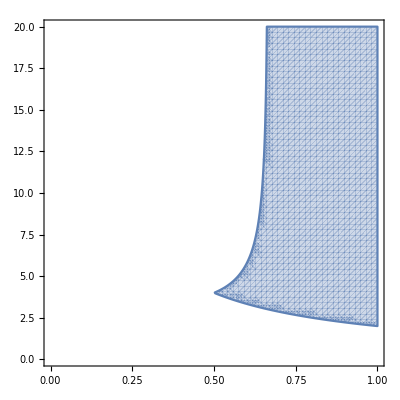

```mathematica
RegionPlot[Evaluate[m=3;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

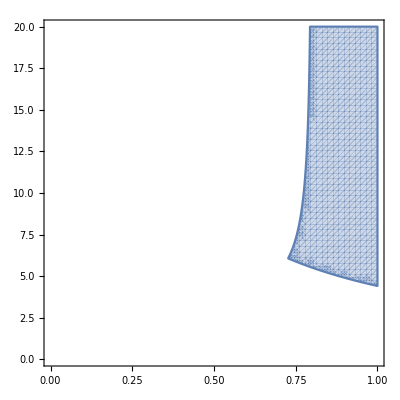

```mathematica
RegionPlot[Evaluate[m=5;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

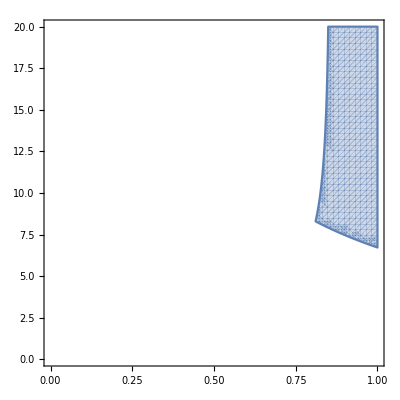

```mathematica
RegionPlot[Evaluate[m=7;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

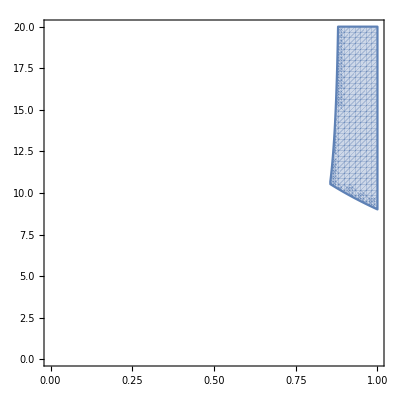

```mathematica
RegionPlot[Evaluate[m=9;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

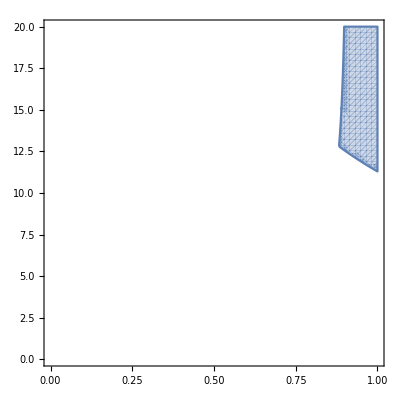

```mathematica
RegionPlot[Evaluate[m=11;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60]
```

```mathematica
Evaluate[m=13;A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]]
```

(θ==1&&Root[-2048-5120 #1^2-4608 #1^4-1792 #1^6-280 #1^8-12 #1^10+#1^11&,1]==ν)||(ν==0&&0≤θ&&θ≤1)||(ν>Root[-4096-4096 #1+5376 #1^2+5376 #1^3-2480 #1^4-2508 #1^5+417 #1^6+351 #1^7-163 #1^8-52 #1^9-11 #1^10+#1^11&,1]&&θ≤1&&Root[4096-2048 ν^2 #1+13312 ν^2 #1^2-5120 ν^4 #1^3+16640 ν^4 #1^4-4608 ν^6 #1^5+9984 ν^6 #1^6-1792 ν^8 #1^7+2912 ν^8 #1^8-280 ν^10 #1^9+364 ν^10 #1^10-12 ν^12 #1^11+13 ν^12 #1^12&,2]≤θ)||(Root[-2048-5120 #1^2-4608 #1^4-1792 #1^6-280 #1^8-12 #1^10+#1^11&,1]<ν&&θ≤1&&ν≤Root[-4096-4096 #1+5376 #1^2+5376 #1^3-2480 #1^4-2508 #1^5+417 #1^6+351 #1^7-163 #1^8-52 #1^9-11 #1^10+#1^11&,1]&&Root[-2048-5120 ν^2 #1^2-4608 ν^4 #1^4-1792 ν^6 #1^6-280 ν^8 #1^8-12 ν^10 #1^10+ν^11 #1^11&,1]≤θ)

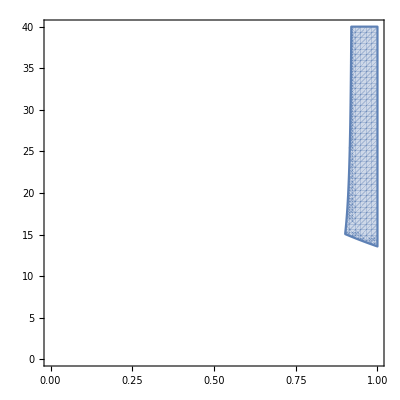

```mathematica
RegionPlot[(θ==1&&Root[-2048-5120 #1^2-4608 #1^4-1792 #1^6-280 #1^8-12 #1^10+#1^11&,1]==ν)||(ν==0&&0≤θ&&θ≤1)||(ν>Root[-4096-4096 #1+5376 #1^2+5376 #1^3-2480 #1^4-2508 #1^5+417 #1^6+351 #1^7-163 #1^8-52 #1^9-11 #1^10+#1^11&,1]&&θ≤1&&Root[4096-2048 ν^2 #1+13312 ν^2 #1^2-5120 ν^4 #1^3+16640 ν^4 #1^4-4608 ν^6 #1^5+9984 ν^6 #1^6-1792 ν^8 #1^7+2912 ν^8 #1^8-280 ν^10 #1^9+364 ν^10 #1^10-12 ν^12 #1^11+13 ν^12 #1^12&,2]≤θ)||(Root[-2048-5120 #1^2-4608 #1^4-1792 #1^6-280 #1^8-12 #1^10+#1^11&,1]<ν&&θ≤1&&ν≤Root[-4096-4096 #1+5376 #1^2+5376 #1^3-2480 #1^4-2508 #1^5+417 #1^6+351 #1^7-163 #1^8-52 #1^9-11 #1^10+#1^11&,1]&&Root[-2048-5120 ν^2 #1^2-4608 ν^4 #1^4-1792 ν^6 #1^6-280 ν^8 #1^8-12 ν^10 #1^10+ν^11 #1^11&,1]≤θ),{θ,0,1},{ν,0,40},PlotPoints->60]
```

### Focusing on entry_(2,1) of the matrix for various odd values of m

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;ExpandDenominator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[2,1]],{m,3,15,2}]
```

{(ν (-2+θ ν))/(4+3 θ^2 ν^2),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (-128-192 θ^2 ν^2-80 θ^4 ν^4-8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (-512-1024 θ^2 ν^2-672 θ^4 ν^4-160 θ^6 ν^6-10 θ^8 ν^8+θ^9 ν^9))/(1024+2816 θ^2 ν^2+2816 θ^4 ν^4+1232 θ^6 ν^6+220 θ^8 ν^8+11 θ^10 ν^10),(ν (-2048-5120 θ^2 ν^2-4608 θ^4 ν^4-1792 θ^6 ν^6-280 θ^8 ν^8-12 θ^10 ν^10+θ^11 ν^11))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(ν (-8192-24576 θ^2 ν^2-28160 θ^4 ν^4-15360 θ^6 ν^6-4032 θ^8 ν^8-448 θ^10 ν^10-14 θ^12 ν^12+θ^13 ν^13))/(16384+61440 θ^2 ν^2+92160 θ^4 ν^4+70400 θ^6 ν^6+28800 θ^8 ν^8+6048 θ^10 ν^10+560 θ^12 ν^12+15 θ^14 ν^14)}

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;ExpandDenominator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,m]],{m,3,15,2}]
```

{(ν (-2+θ ν))/(4+3 θ^2 ν^2),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (-128-192 θ^2 ν^2-80 θ^4 ν^4-8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (-512-1024 θ^2 ν^2-672 θ^4 ν^4-160 θ^6 ν^6-10 θ^8 ν^8+θ^9 ν^9))/(1024+2816 θ^2 ν^2+2816 θ^4 ν^4+1232 θ^6 ν^6+220 θ^8 ν^8+11 θ^10 ν^10),(ν (-2048-5120 θ^2 ν^2-4608 θ^4 ν^4-1792 θ^6 ν^6-280 θ^8 ν^8-12 θ^10 ν^10+θ^11 ν^11))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(ν (-8192-24576 θ^2 ν^2-28160 θ^4 ν^4-15360 θ^6 ν^6-4032 θ^8 ν^8-448 θ^10 ν^10-14 θ^12 ν^12+θ^13 ν^13))/(16384+61440 θ^2 ν^2+92160 θ^4 ν^4+70400 θ^6 ν^6+28800 θ^8 ν^8+6048 θ^10 ν^10+560 θ^12 ν^12+15 θ^14 ν^14)}

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;ExpandDenominator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,2]],{m,3,15,2}]
```

{(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (32+32 θ^2 ν^2+6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (128+192 θ^2 ν^2+80 θ^4 ν^4+8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (512+1024 θ^2 ν^2+672 θ^4 ν^4+160 θ^6 ν^6+10 θ^8 ν^8+θ^9 ν^9))/(1024+2816 θ^2 ν^2+2816 θ^4 ν^4+1232 θ^6 ν^6+220 θ^8 ν^8+11 θ^10 ν^10),(ν (2048+5120 θ^2 ν^2+4608 θ^4 ν^4+1792 θ^6 ν^6+280 θ^8 ν^8+12 θ^10 ν^10+θ^11 ν^11))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(ν (8192+24576 θ^2 ν^2+28160 θ^4 ν^4+15360 θ^6 ν^6+4032 θ^8 ν^8+448 θ^10 ν^10+14 θ^12 ν^12+θ^13 ν^13))/(16384+61440 θ^2 ν^2+92160 θ^4 ν^4+70400 θ^6 ν^6+28800 θ^8 ν^8+6048 θ^10 ν^10+560 θ^12 ν^12+15 θ^14 ν^14)}

### The θ=0 case is clear, see below. So in what follows we can assume: 0<θ≤1. Also, for ν=0, the corresponding matrix is the identity matrix, so we can assume in what follows that ν>0.

```mathematica
With[{θ=0},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,3,9,2}]]
```

{(1 | ν/2 | -ν/2
-ν/2 | 1 | ν/2
ν/2 | -ν/2 | 1),(1 | ν/2 | 0 | 0 | -ν/2
-ν/2 | 1 | ν/2 | 0 | 0
0 | -ν/2 | 1 | ν/2 | 0
0 | 0 | -ν/2 | 1 | ν/2
ν/2 | 0 | 0 | -ν/2 | 1),(1 | ν/2 | 0 | 0 | 0 | 0 | -ν/2
-ν/2 | 1 | ν/2 | 0 | 0 | 0 | 0
0 | -ν/2 | 1 | ν/2 | 0 | 0 | 0
0 | 0 | -ν/2 | 1 | ν/2 | 0 | 0
0 | 0 | 0 | -ν/2 | 1 | ν/2 | 0
0 | 0 | 0 | 0 | -ν/2 | 1 | ν/2
ν/2 | 0 | 0 | 0 | 0 | -ν/2 | 1),(1 | ν/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ν/2
-ν/2 | 1 | ν/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ν/2 | 1 | ν/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ν/2 | 1 | ν/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ν/2 | 1 | ν/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ν/2 | 1 | ν/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ν/2 | 1 | ν/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ν/2 | 1 | ν/2
ν/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ν/2 | 1)}

### Useful fact: the sum/product/inverse of circulant matrices is circulant [REFERENCE: Fact 5.16.7. in Berstein MATRIX MATHEMATICS]. Since A is circulant, the matrix Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A) is circulant, too.

### These are the denominators of the first row of the θ-matrix for various odd values of m; that is, the determinant of the matrix IdentityMatrix[Length[A]]-θ ν A

```mathematica
With[{θ=θ},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Expand@Det[IdentityMatrix[Length[A]]-θ ν A],{m,3,15,2}]]
```

{1+(3 θ^2 ν^2)/4,1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16,1+(7 θ^2 ν^2)/4+(7 θ^4 ν^4)/8+(7 θ^6 ν^6)/64,1+(9 θ^2 ν^2)/4+(27 θ^4 ν^4)/16+(15 θ^6 ν^6)/32+(9 θ^8 ν^8)/256,1+(11 θ^2 ν^2)/4+(11 θ^4 ν^4)/4+(77 θ^6 ν^6)/64+(55 θ^8 ν^8)/256+(11 θ^10 ν^10)/1024,1+(13 θ^2 ν^2)/4+(65 θ^4 ν^4)/16+(39 θ^6 ν^6)/16+(91 θ^8 ν^8)/128+(91 θ^10 ν^10)/1024+(13 θ^12 ν^12)/4096,1+(15 θ^2 ν^2)/4+(45 θ^4 ν^4)/8+(275 θ^6 ν^6)/64+(225 θ^8 ν^8)/128+(189 θ^10 ν^10)/512+(35 θ^12 ν^12)/1024+(15 θ^14 ν^14)/16384}

```mathematica
With[{θ=θ},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm[IdentityMatrix[Length[A]]-θ ν A],{m,3,9,2}]]
```

{(1 | -(θ ν)/2 | (θ ν)/2
(θ ν)/2 | 1 | -(θ ν)/2
-(θ ν)/2 | (θ ν)/2 | 1),(1 | -(θ ν)/2 | 0 | 0 | (θ ν)/2
(θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0
0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0
0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2
-(θ ν)/2 | 0 | 0 | (θ ν)/2 | 1),(1 | -(θ ν)/2 | 0 | 0 | 0 | 0 | (θ ν)/2
(θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0 | 0
0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0
0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0
0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0
0 | 0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2
-(θ ν)/2 | 0 | 0 | 0 | 0 | (θ ν)/2 | 1),(1 | -(θ ν)/2 | 0 | 0 | 0 | 0 | 0 | 0 | (θ ν)/2
(θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | (θ ν)/2 | 1 | -(θ ν)/2
-(θ ν)/2 | 0 | 0 | 0 | 0 | 0 | 0 | (θ ν)/2 | 1)}

### Notation: μ:=(ν θ)^2>0, that is, ν→(√μ)/θ

```mathematica
{1+(3 θ^2 ν^2)/4,1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16,1+(7 θ^2 ν^2)/4+(7 θ^4 ν^4)/8+(7 θ^6 ν^6)/64,1+(9 θ^2 ν^2)/4+(27 θ^4 ν^4)/16+(15 θ^6 ν^6)/32+(9 θ^8 ν^8)/256,1+(11 θ^2 ν^2)/4+(11 θ^4 ν^4)/4+(77 θ^6 ν^6)/64+(55 θ^8 ν^8)/256+(11 θ^10 ν^10)/1024,1+(13 θ^2 ν^2)/4+(65 θ^4 ν^4)/16+(39 θ^6 ν^6)/16+(91 θ^8 ν^8)/128+(91 θ^10 ν^10)/1024+(13 θ^12 ν^12)/4096,1+(15 θ^2 ν^2)/4+(45 θ^4 ν^4)/8+(275 θ^6 ν^6)/64+(225 θ^8 ν^8)/128+(189 θ^10 ν^10)/512+(35 θ^12 ν^12)/1024+(15 θ^14 ν^14)/16384}/.ν->(√μ)/θ
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}

### The denominators of the full matrix Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A) satisfy a second-order linear recurrence relation as a function of m=2k+1; we need to prove positivity for all of them for ν>0, 0<θ≤1. These denominators are the determinants of IdentityMatrix[Length[A]]-θ ν A The form of the linear recurrence must follow from recursive determinant expansions of the following kind:

```mathematica
Det[({{1, -(√μ)/2, 0, 0, 0, 0, 0, 0, (√μ)/2}, {(√μ)/2, 1, -(√μ)/2, 0, 0, 0, 0, 0, 0}, {0, (√μ)/2, 1, -(√μ)/2, 0, 0, 0, 0, 0}, {0, 0, (√μ)/2, 1, -(√μ)/2, 0, 0, 0, 0}, {0, 0, 0, (√μ)/2, 1, -(√μ)/2, 0, 0, 0}, {0, 0, 0, 0, (√μ)/2, 1, -(√μ)/2, 0, 0}, {0, 0, 0, 0, 0, (√μ)/2, 1, -(√μ)/2, 0}, {0, 0, 0, 0, 0, 0, (√μ)/2, 1, -(√μ)/2}, {-(√μ)/2, 0, 0, 0, 0, 0, 0, (√μ)/2, 1}})]==(1+μ/2) Det[({{1, -(√μ)/2, 0, 0, 0, 0, (√μ)/2}, {(√μ)/2, 1, -(√μ)/2, 0, 0, 0, 0}, {0, (√μ)/2, 1, -(√μ)/2, 0, 0, 0}, {0, 0, (√μ)/2, 1, -(√μ)/2, 0, 0}, {0, 0, 0, (√μ)/2, 1, -(√μ)/2, 0}, {0, 0, 0, 0, (√μ)/2, 1, -(√μ)/2}, {-(√μ)/2, 0, 0, 0, 0, (√μ)/2, 1}})]-1/16 μ^2 Det[({{1, -(√μ)/2, 0, 0, (√μ)/2}, {(√μ)/2, 1, -(√μ)/2, 0, 0}, {0, (√μ)/2, 1, -(√μ)/2, 0}, {0, 0, (√μ)/2, 1, -(√μ)/2}, {-(√μ)/2, 0, 0, (√μ)/2, 1}})]//Simplify
```

True

```mathematica
Expand@FindLinearRecurrence[{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}]
```

{1+μ/2,-μ^2/16}

### When writing down this in the manuscript, SHIFT the index by 1, so denom[1]==1+(3 μ)/4,denom[2]==1+(5 μ)/4+(5 μ^2)/16

```mathematica
RecurrenceTable[{denom[k+2]== (1+μ/2)denom[k+1]-μ^2/16 denom[k],denom[1]==1,denom[2]==1+(3 μ)/4},denom,{k,2,8}]//Expand
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}

```mathematica
RSolve[{denom[k+2]== (1+μ/2)denom[k+1]-μ^2/16 denom[k],denom[1]==1,denom[2]==1+(3 μ)/4},denom[k],k]
```

```mathematica
{{denom[k]->-(2^(1-2 k) ((2+μ-2 √(1+μ))^k+μ (2+μ-2 √(1+μ))^k+√(1+μ) (2+μ-2 √(1+μ))^k-(2+μ+2 √(1+μ))^k-μ (2+μ+2 √(1+μ))^k+√(1+μ) (2+μ+2 √(1+μ))^k))/(μ √(1+μ))}}//Apart//Simplify
```

```mathematica
{{denom[k]->-(2^(1-2 k) ((2+μ-2 √(1+μ))^k+√(1+μ) (2+μ-2 √(1+μ))^k+(2+μ+2 √(1+μ))^k-√(1+μ) (2+μ+2 √(1+μ))^k))/μ}}
```

```mathematica
{{denom[k]->-(2^(1-2 k) ((2+μ-2 √(1+μ))^k (1+√(1+μ))+-(-1+√(1+μ)) (2+μ+2 √(1+μ))^k))/μ}}
```

```mathematica
-(2^(1-2 k) ((2+μ-2 √(1+μ))^k (1+√(1+μ))+(1-√(1+μ)) (2+μ+2 √(1+μ))^k))/μ//TeXForm
```

-\frac{2^{1-2 k} \left(\left(\sqrt{\mu +1}+1\right) \left(\mu -2 \sqrt{\mu +1}+2\right)^k+\left(1-\sqrt{\mu +1}\right) \left(\mu +2 \sqrt{\mu
   +1}+2\right)^k\right)}{\mu }

Notice that 2+μ+2 √(1+μ)==(1+√(1+μ))^2 and 2+μ-2 √(1+μ)==(1-√(1+μ))^2, so

```mathematica
{{denom[k]->-(2^(1-2 k) (((1-√(1+μ))^2)^k+√(1+μ) ((1-√(1+μ))^2)^k+((1+√(1+μ))^2)^k-√(1+μ) ((1+√(1+μ))^2)^k))/μ}}//PowerExpand
```

```mathematica
{{denom[k]->-(2^(1-2 k) ((1-√(1+μ))^(2 k)+√(1+μ) (1-√(1+μ))^(2 k)+(1+√(1+μ))^(2 k)-√(1+μ) (1+√(1+μ))^(2 k)))/μ}}
```

```mathematica
{{denom[k]->-(2^(1-2 k) ((1-√(1+μ))^(2 k) (1+√(1+μ))-(-1+√(1+μ)) (1+√(1+μ))^(2 k)))/μ}}
```

```mathematica
Solve[λ^2-(1+μ/2)λ+μ^2/16==0,λ]
```

{{λ→1/4 (2+μ-2 √(1+μ))},{λ→1/4 (2+μ+2 √(1+μ))}}

Notice that

```mathematica
1+√(1+μ)==μ/(√(1+μ)-1)//TeXForm
```

\sqrt{\mu +1}+1=\frac{\mu }{\sqrt{\mu +1}-1}

```mathematica
1+√(1+μ)==μ/(√(1+μ)-1)//Simplify
```

True

so

```mathematica
{{denom[k]->-(2^(1-2 k) ((1-√(1+μ))^(2 k) (μ/(√(1+μ)-1))-(-1+√(1+μ)) (μ/(√(1+μ)-1))^(2 k)))/μ}}//PowerExpand
```

{{denom[k]→-(2^(1-2 k) ((μ (1-√(1+μ))^(2 k))/(-1+√(1+μ))-μ^(2 k) (-1+√(1+μ))^(1-2 k)))/μ}}

```mathematica
{{denom[k]->(2^(1-2 k) (-(μ (1-√(1+μ))^(2 k))/(-1+√(1+μ))+μ^(2 k) (-1+√(1+μ))^(1-2 k)))/μ}}
```

```mathematica
{{denom[k]->(2^(1-2 k) (-(μ (1-√(1+μ))^(2 k))/(-1+√(1+μ))))/μ+(2^(1-2 k) (+μ^(2 k) (-1+√(1+μ))^(1-2 k)))/μ}}
```

```mathematica
{{denom[k]->-(2^(1-2 k) (1-√(1+μ))^(2 k))/(-1+√(1+μ))+2^(1-2 k) μ^(-1+2 k) (-1+√(1+μ))^(1-2 k)}}//Simplify
```

```mathematica
{{denom[k]->(2^(1-2 k) (-(1-√(1+μ))^(2 k)+μ^(-1+2 k) (-1+√(1+μ))^(2-2 k)))/(-1+√(1+μ))}}
```

```mathematica
{{denom[k]->2^(1-2 k)/(√(1+μ)-1) ((√(1+μ)-1)μ^(-1+2 k) (√(1+μ)-1)^(1-2 k)-(1-√(1+μ))^(2 k))}}
```

```mathematica
{{denom[k]->2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))}}
```

Check:

```mathematica
2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->1//Simplify
```

1

```mathematica
2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->2//Simplify
```

1+(3 μ)/4

```mathematica
(2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->k+2)==(1+μ/2)(2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->k+1)-μ^2/16(2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1)))//Simplify
```

True

```mathematica
Table[2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))//Expand,{k,2,8}]
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}

```mathematica
{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384}

```mathematica
2^(1-2 k) ((√(1+μ)+1)^(2 k-1)-(√(1+μ)-1)^(2 k-1))/.k->k+1//Simplify
```

2^(-1-2 k) (-(-1+√(1+μ))^(1+2 k)+(1+√(1+μ))^(1+2 k))

```mathematica
Table[2^(-1-2 k) (-(-1+√(1+μ))^(1+2 k)+(1+√(1+μ))^(1+2 k))//Expand,{k,1,8}]
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384,1+(17 μ)/4+(119 μ^2)/16+(221 μ^3)/32+(935 μ^4)/256+(561 μ^5)/512+(357 μ^6)/2048+(51 μ^7)/4096+(17 μ^8)/65536}

### This is the explicit form: ((√(1+μ)+1)/2)^(2 k+1)-((√(1+μ)-1)/2)^(2 k+1) ; k=1 corresponds to the matrix size m=2k+1=3.

Since (√(1+μ)+1)/2>(√(1+μ)-1)/2>0, this clearly shows that all the determinants are positive, for any k≥1,1≥θ>0, ν>0, that is, with μ:=(ν θ )^2>0.

```mathematica
Table[((√(1+μ)+1)/2)^(2 k+1)-((√(1+μ)-1)/2)^(2 k+1)//Expand,{k,1,8}]
```

{1+(3 μ)/4,1+(5 μ)/4+(5 μ^2)/16,1+(7 μ)/4+(7 μ^2)/8+(7 μ^3)/64,1+(9 μ)/4+(27 μ^2)/16+(15 μ^3)/32+(9 μ^4)/256,1+(11 μ)/4+(11 μ^2)/4+(77 μ^3)/64+(55 μ^4)/256+(11 μ^5)/1024,1+(13 μ)/4+(65 μ^2)/16+(39 μ^3)/16+(91 μ^4)/128+(91 μ^5)/1024+(13 μ^6)/4096,1+(15 μ)/4+(45 μ^2)/8+(275 μ^3)/64+(225 μ^4)/128+(189 μ^5)/512+(35 μ^6)/1024+(15 μ^7)/16384,1+(17 μ)/4+(119 μ^2)/16+(221 μ^3)/32+(935 μ^4)/256+(561 μ^5)/512+(357 μ^6)/2048+(51 μ^7)/4096+(17 μ^8)/65536}

```mathematica
((√(1+μ)+1)/2)^(2 k+1)-((√(1+μ)-1)/2)^(2 k+1)//TeXForm
```

2^{-2 k-1} \left(\sqrt{\mu +1}+1\right)^{2 k+1}-2^{-2 k-1} \left(\sqrt{\mu +1}-1\right)^{2 k+1}

```mathematica
Simplify[-(2^(1-2 k) ((2+μ-2 √(1+μ))^k (1+√(1+μ))+(1-√(1+μ)) (2+μ+2 √(1+μ))^k))/μ/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

```mathematica
((-1+y^2)^(1-2 k) (-y^2+y^(4 k)))/y^2
```

```mathematica
((1-y^2)^(1-2 k) y^2(1-y^(4 k-2)))/y^2
```

```mathematica
(1-y^2)^(1-2 k) (1-y^(-2+4 k))//TeXForm
```

\left(1-y^2\right)^{1-2 k} \left(1-y^{4 k-2}\right)

```mathematica
Simplify[((√(1+μ)+1)/2)^(2 k+1)-((√(1+μ)-1)/2)^(2 k+1)/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

(-1+y^2)^(-1-2 k) (-1+y^(2+4 k))

```mathematica
(-1+y^2)^(-1-2 k) (-1+y^(2+4 k))
```

```mathematica
(1-y^2)^(-1-2 k) (1-y^(2+4 k))==(1-y^2)^(1-2 k) (1-y^(-2+4 k))
```

```mathematica
(1-y^2)^-1 (1-y^(2+4 k))==(1-y^2)^1 (1-y^(-2+4 k))
```

```mathematica
(1-y^(2+4 k))/(1-y^2)==(1-y^2) (1-y^(-2+4 k))
```

```mathematica
(1-y^(2+4 k))/1==(1-y^2)(1-y^2) (1-y^(-2+4 k))
```

```mathematica
1-y^(2+4 k)==(1-y^2)^2 (1-y^(-2+4 k))//Simplify
```

y^5+2 y^(1+4 k)==2 y^3+y^(-1+4 k)

```mathematica
((-1+y^2)^(1-2 k) (-y^2+y^(4 k)))/y^2==(-1+y^2)^(-1-2 k) (-1+y^(2+4 k))//Simplify
```

```mathematica
((-1+y^2)^(-1-2 k) (-2 y^4+y^6-y^(4 k)+2 y^(2+4 k)))/y==0/.k->2//Simplify
```

(y (2+y^2+2 y^4))/(-1+y^2)==0

```mathematica
((√(1+μ)+1)/2)^(2 k+1)-((√(1+μ)-1)/2)^(2 k+1)/.k->1//Simplify
```

1+(3 μ)/4

```mathematica
RSolve[{denom[k+2]== (1+μ/2)denom[k+1]-μ^2/16 denom[k],denom[1]==1+(3 μ)/4,denom[2]==1+(5 μ)/4+(5 μ^2)/16},denom[k],k]
```

{{denom[k]→(2^(-1-2 k) (-(2+μ-2 √(1+μ))^k-μ (2+μ-2 √(1+μ))^k+√(1+μ) (2+μ-2 √(1+μ))^k+(2+μ+2 √(1+μ))^k+μ (2+μ+2 √(1+μ))^k+√(1+μ) (2+μ+2 √(1+μ))^k))/(√(1+μ))}}

```mathematica
(2^(-1-2 k) (-(2+μ-2 √(1+μ))^k-μ (2+μ-2 √(1+μ))^k+√(1+μ) (2+μ-2 √(1+μ))^k+(2+μ+2 √(1+μ))^k+μ (2+μ+2 √(1+μ))^k+√(1+μ) (2+μ+2 √(1+μ))^k))/(√(1+μ))//Simplify
```

(2^(-1-2 k) (-(2+μ-2 √(1+μ))^k+√(1+μ) (2+μ-2 √(1+μ))^k+(2+μ+2 √(1+μ))^k+√(1+μ) (2+μ+2 √(1+μ))^k+μ (-(2+μ-2 √(1+μ))^k+(2+μ+2 √(1+μ))^k)))/(√(1+μ))

```mathematica
Simplify[(2^(-1-2 k) (-(2+μ-2 √(1+μ))^k+√(1+μ) (2+μ-2 √(1+μ))^k+(2+μ+2 √(1+μ))^k+√(1+μ) (2+μ+2 √(1+μ))^k+μ (-(2+μ-2 √(1+μ))^k+(2+μ+2 √(1+μ))^k)))/(√(1+μ))/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

```mathematica
(-1+y^2)^(-1-2 k) (-1+y^(2+4 k))//Simplify
```

```mathematica
(-1+y^2)^(-1-2 k) (-1+y^(2+4 k))
```

```mathematica
(1-y^2)^(-1-2 k) (1-y^(2+4 k))
```

```mathematica
(1-y^2)^(-1-2 k) (1-(y^(1+2 k))^2)
```

```mathematica
(1-y^2)^(-1-2 k) (1-(y^(1+2 k)))(1+(y^(1+2 k)))
```

(1-y^2)^(-1-2 k) (1-y^(1+2 k)) (1+y^(1+2 k))

```mathematica
(1-y^2)^(-1-2 k) (1-y^(2+4 k))/.y-> (√(1+μ)-1)/(√μ)//Simplify
```

```mathematica
(1-(-1+√(1+μ))^2/μ)^(-1-2 k) (1-((-1+√(1+μ))/(√μ))^(2+4 k))/.k->2//Simplify
```

1+(5 μ)/4+(5 μ^2)/16

### Similarly, there seems to be just two kinds of recurrences as a function of m=2k+1 for the polynomials in the numerators (but with different starting values)

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,m]],{m,3,15,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,1]],{m,3,15,2}]
```

{2 (2+θ^2 ν^2),-θ^4 ν^4}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,2]],{m,3,15,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[2,1]],{m,3,15,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,3]],{m,3,15,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
FindLinearRecurrence@Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Numerator@Factor@Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,4]],{m,5,17,2}]
```

{4+3 θ^2 ν^2,-4 θ^2 ν^2-3 θ^4 ν^4,θ^6 ν^6}

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)],{m,3,5,2}]
```

{{{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (-2+θ ν))/(4+3 θ^2 ν^2)},{(ν (-2+θ ν))/(4+3 θ^2 ν^2),(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(ν (2+θ ν))/(4+3 θ^2 ν^2)},{(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (-2+θ ν))/(4+3 θ^2 ν^2),(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2)}},{{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4)}}}

### Just considering the 1st row of some matrices for different odd values of m:

```mathematica
Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9,2}]
```

{{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (-2+θ ν))/(4+3 θ^2 ν^2)},{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(64-32 θ ν^2+112 θ^2 ν^2-32 θ^3 ν^4+56 θ^4 ν^4-6 θ^5 ν^6+7 θ^6 ν^6)/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (32+32 θ^2 ν^2+6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ ν^2 (16+12 θ^2 ν^2-2 θ^3 ν^3+θ^4 ν^4))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ^2 ν^3 (8+4 θ ν+4 θ^2 ν^2+θ^3 ν^3))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ^2 ν^3 (-8+4 θ ν-4 θ^2 ν^2+θ^3 ν^3))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ ν^2 (16+12 θ^2 ν^2+2 θ^3 ν^3+θ^4 ν^4))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6)},{(256-128 θ ν^2+576 θ^2 ν^2-192 θ^3 ν^4+432 θ^4 ν^4-80 θ^5 ν^6+120 θ^6 ν^6-8 θ^7 ν^8+9 θ^8 ν^8)/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (128+192 θ^2 ν^2+80 θ^4 ν^4+8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ ν^2 (64+80 θ^2 ν^2+24 θ^4 ν^4-2 θ^5 ν^5+θ^6 ν^6))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ^2 ν^3 (32+32 θ^2 ν^2+4 θ^3 ν^3+6 θ^4 ν^4+θ^5 ν^5))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ^3 ν^4 (16-8 θ ν+12 θ^2 ν^2-4 θ^3 ν^3+θ^4 ν^4))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ^3 ν^4 (16+8 θ ν+12 θ^2 ν^2+4 θ^3 ν^3+θ^4 ν^4))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ^2 ν^3 (-32-32 θ^2 ν^2+4 θ^3 ν^3-6 θ^4 ν^4+θ^5 ν^5))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(θ ν^2 (64+80 θ^2 ν^2+24 θ^4 ν^4+2 θ^5 ν^5+θ^6 ν^6))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8),(ν (-128-192 θ^2 ν^2-80 θ^4 ν^4-8 θ^6 ν^6+θ^7 ν^7))/(256+576 θ^2 ν^2+432 θ^4 ν^4+120 θ^6 ν^6+9 θ^8 ν^8)}}

# Focusing on the θ=1/2 special case: we get the “negative” result by comparing the numerators of the first and last entries of the first row of the matrix of odd size (assuming that the denominators are positive).

```mathematica
With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9}]]
```

{{(16-ν^2)/(16+3 ν^2),(2 ν (4+ν))/(16+3 ν^2),(2 (-4+ν) ν)/(16+3 ν^2)},{4/(4+ν^2),(2 ν)/(4+ν^2),ν^2/(4+ν^2),-(2 ν)/(4+ν^2)},{(256+16 ν^2-3 ν^4)/(256+80 ν^2+5 ν^4),(2 ν (64+8 ν^2+ν^3))/(256+80 ν^2+5 ν^4),(2 ν^2 (16-4 ν+ν^2))/(256+80 ν^2+5 ν^4),(2 ν^2 (16+4 ν+ν^2))/(256+80 ν^2+5 ν^4),(2 ν (-64-8 ν^2+ν^3))/(256+80 ν^2+5 ν^4)},{(16-ν^2)/(16+3 ν^2),(8 ν)/(16+3 ν^2),(2 ν^2)/(16+3 ν^2),0,(2 ν^2)/(16+3 ν^2),-(8 ν)/(16+3 ν^2)},{(4096+768 ν^2-32 ν^4-5 ν^6)/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν (1024+256 ν^2+12 ν^4+ν^5))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^2 (256+48 ν^2-4 ν^3+ν^4))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^3 (64+16 ν+8 ν^2+ν^3))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^3 (-64+16 ν-8 ν^2+ν^3))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^2 (256+48 ν^2+4 ν^3+ν^4))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν (-1024-256 ν^2-12 ν^4+ν^5))/(4096+1792 ν^2+224 ν^4+7 ν^6)},{(64+8 ν^2-ν^4)/(64+24 ν^2+2 ν^4),(ν (16+3 ν^2))/(32+12 ν^2+ν^4),ν^2/(8+2 ν^2),ν^3/(32+12 ν^2+ν^4),ν^4/(64+24 ν^2+2 ν^4),-ν^3/(32+12 ν^2+ν^4),ν^2/(8+2 ν^2),-(ν (16+3 ν^2))/(32+12 ν^2+ν^4)},{(65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8)/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν (16384+6144 ν^2+640 ν^4+16 ν^6+ν^7))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^2 (4096+1280 ν^2+96 ν^4-4 ν^5+ν^6))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^3 (1024+256 ν^2+16 ν^3+12 ν^4+ν^5))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^4 (256-64 ν+48 ν^2-8 ν^3+ν^4))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^4 (256+64 ν+48 ν^2+8 ν^3+ν^4))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^3 (-1024-256 ν^2+16 ν^3-12 ν^4+ν^5))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^2 (4096+1280 ν^2+96 ν^4+4 ν^5+ν^6))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8)}}

```mathematica
With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9,2}]]
```

{{(16-ν^2)/(16+3 ν^2),(2 ν (4+ν))/(16+3 ν^2),(2 (-4+ν) ν)/(16+3 ν^2)},{(256+16 ν^2-3 ν^4)/(256+80 ν^2+5 ν^4),(2 ν (64+8 ν^2+ν^3))/(256+80 ν^2+5 ν^4),(2 ν^2 (16-4 ν+ν^2))/(256+80 ν^2+5 ν^4),(2 ν^2 (16+4 ν+ν^2))/(256+80 ν^2+5 ν^4),(2 ν (-64-8 ν^2+ν^3))/(256+80 ν^2+5 ν^4)},{(4096+768 ν^2-32 ν^4-5 ν^6)/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν (1024+256 ν^2+12 ν^4+ν^5))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^2 (256+48 ν^2-4 ν^3+ν^4))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^3 (64+16 ν+8 ν^2+ν^3))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^3 (-64+16 ν-8 ν^2+ν^3))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν^2 (256+48 ν^2+4 ν^3+ν^4))/(4096+1792 ν^2+224 ν^4+7 ν^6),(2 ν (-1024-256 ν^2-12 ν^4+ν^5))/(4096+1792 ν^2+224 ν^4+7 ν^6)},{(65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8)/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν (16384+6144 ν^2+640 ν^4+16 ν^6+ν^7))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^2 (4096+1280 ν^2+96 ν^4-4 ν^5+ν^6))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^3 (1024+256 ν^2+16 ν^3+12 ν^4+ν^5))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^4 (256-64 ν+48 ν^2-8 ν^3+ν^4))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^4 (256+64 ν+48 ν^2+8 ν^3+ν^4))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^3 (-1024-256 ν^2+16 ν^3-12 ν^4+ν^5))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν^2 (4096+1280 ν^2+96 ν^4+4 ν^5+ν^6))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8),(2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7))/(65536+36864 ν^2+6912 ν^4+480 ν^6+9 ν^8)}}

```mathematica
Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9,2}]]
```

{{16-ν^2,2 ν (4+ν),2 (-4+ν) ν},{256+16 ν^2-3 ν^4,2 ν (64+8 ν^2+ν^3),2 ν^2 (16-4 ν+ν^2),2 ν^2 (16+4 ν+ν^2),2 ν (-64-8 ν^2+ν^3)},{4096+768 ν^2-32 ν^4-5 ν^6,2 ν (1024+256 ν^2+12 ν^4+ν^5),2 ν^2 (256+48 ν^2-4 ν^3+ν^4),2 ν^3 (64+16 ν+8 ν^2+ν^3),2 ν^3 (-64+16 ν-8 ν^2+ν^3),2 ν^2 (256+48 ν^2+4 ν^3+ν^4),2 ν (-1024-256 ν^2-12 ν^4+ν^5)},{65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8,2 ν (16384+6144 ν^2+640 ν^4+16 ν^6+ν^7),2 ν^2 (4096+1280 ν^2+96 ν^4-4 ν^5+ν^6),2 ν^3 (1024+256 ν^2+16 ν^3+12 ν^4+ν^5),2 ν^4 (256-64 ν+48 ν^2-8 ν^3+ν^4),2 ν^4 (256+64 ν+48 ν^2+8 ν^3+ν^4),2 ν^3 (-1024-256 ν^2+16 ν^3-12 ν^4+ν^5),2 ν^2 (4096+1280 ν^2+96 ν^4+4 ν^5+ν^6),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7)}}

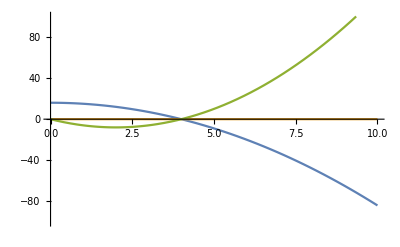

```mathematica
Plot[{16-ν^2,0 2 ν (4+ν),2 (-4+ν) ν},{ν,0,10},PlotRange->{-100,100}]
```

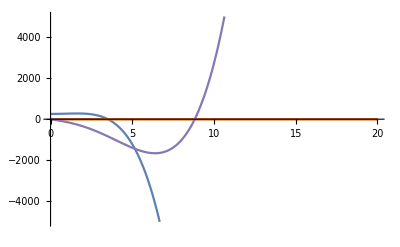

```mathematica
Plot[{256+16 ν^2-3 ν^4,0 2 ν (64+8 ν^2+ν^3),0 2 ν^2 (16-4 ν+ν^2),0 2 ν^2 (16+4 ν+ν^2),2 ν (-64-8 ν^2+ν^3)},{ν,0,20},PlotRange->{-5000,5000}]
```

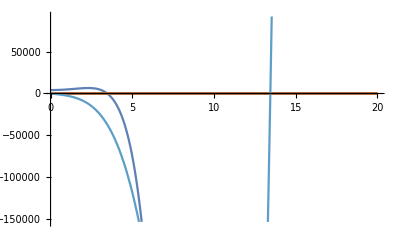

```mathematica
Plot[{4096+768 ν^2-32 ν^4-5 ν^6,0 2 ν (1024+256 ν^2+12 ν^4+ν^5),0 2 ν^2 (256+48 ν^2-4 ν^3+ν^4),0 2 ν^3 (64+16 ν+8 ν^2+ν^3),0 2 ν^3 (-64+16 ν-8 ν^2+ν^3), 0 2 ν^2 (256+48 ν^2+4 ν^3+ν^4),2 ν (-1024-256 ν^2-12 ν^4+ν^5)},{ν,0,20}]
```

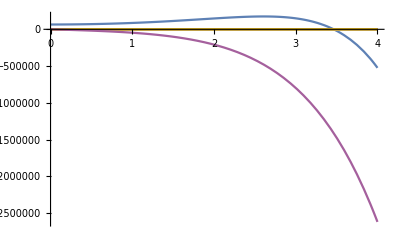

```mathematica
Plot[{65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8,0 2 ν (16384+6144 ν^2+640 ν^4+16 ν^6+ν^7),0 2 ν^2 (4096+1280 ν^2+96 ν^4-4 ν^5+ν^6),0 2 ν^3 (1024+256 ν^2+16 ν^3+12 ν^4+ν^5),0 2 ν^4 (256-64 ν+48 ν^2-8 ν^3+ν^4),0 2 ν^4 (256+64 ν+48 ν^2+8 ν^3+ν^4),0 2 ν^3 (-1024-256 ν^2+16 ν^3-12 ν^4+ν^5),0 2 ν^2 (4096+1280 ν^2+96 ν^4+4 ν^5+ν^6),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7)},{ν,0,4}]
```

```mathematica
Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,1]],{m,3,17,2}]]
```

{16-ν^2,256+16 ν^2-3 ν^4,4096+768 ν^2-32 ν^4-5 ν^6,65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8,1048576+458752 ν^2+49152 ν^4-1792 ν^6-400 ν^8-9 ν^10,16777216+9437184 ν^2+1638400 ν^4+49152 ν^6-10752 ν^8-784 ν^10-11 ν^12,268435456+184549376 ν^2+44040192 ν^4+3604480 ν^6-122880 ν^8-32256 ν^10-1344 ν^12-13 ν^14,4294967296+3489660928 ν^2+1056964608 ν^4+136314880 ν^6+3604480 ν^8-811008 ν^10-75264 ν^12-2112 ν^14-15 ν^16}

```mathematica
FindLinearRecurrence[Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,1]],{m,3,15,2}]]]
```

{2 (8+ν^2),-ν^4}

```mathematica
RSolve[{topleftpoly[n+2]==2 (8+ν^2)topleftpoly[n+1]-ν^4  topleftpoly[n],topleftpoly[0]==1,topleftpoly[1]==16-ν^2 },topleftpoly[n],n]
```

{{topleftpoly[n]→(-4 (8+ν^2-4 √(4+ν^2))^n+ν^2 (8+ν^2-4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2-4 √(4+ν^2))^n+4 (8+ν^2+4 √(4+ν^2))^n-ν^2 (8+ν^2+4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2+4 √(4+ν^2))^n)/(4 √(4+ν^2))}}

```mathematica
Table[(-4 (8+ν^2-4 √(4+ν^2))^n+ν^2 (8+ν^2-4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2-4 √(4+ν^2))^n+4 (8+ν^2+4 √(4+ν^2))^n-ν^2 (8+ν^2+4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2+4 √(4+ν^2))^n)/(4 √(4+ν^2))//Simplify,{n,1,8}]
```

{16-ν^2,256+16 ν^2-3 ν^4,4096+768 ν^2-32 ν^4-5 ν^6,65536+20480 ν^2+768 ν^4-160 ν^6-7 ν^8,1048576+458752 ν^2+49152 ν^4-1792 ν^6-400 ν^8-9 ν^10,16777216+9437184 ν^2+1638400 ν^4+49152 ν^6-10752 ν^8-784 ν^10-11 ν^12,268435456+184549376 ν^2+44040192 ν^4+3604480 ν^6-122880 ν^8-32256 ν^10-1344 ν^12-13 ν^14,4294967296+3489660928 ν^2+1056964608 ν^4+136314880 ν^6+3604480 ν^8-811008 ν^10-75264 ν^12-2112 ν^14-15 ν^16}

```mathematica
%89==%97
```

True

```mathematica
Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,m]],{m,3,15,2}]]
```

{2 (-4+ν) ν,2 ν (-64-8 ν^2+ν^3),2 ν (-1024-256 ν^2-12 ν^4+ν^5),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7),2 ν (-262144-131072 ν^2-21504 ν^4-1280 ν^6-20 ν^8+ν^9),2 ν (-4194304-2621440 ν^2-589824 ν^4-57344 ν^6-2240 ν^8-24 ν^10+ν^11),-2 ν (67108864+50331648 ν^2+14417920 ν^4+1966080 ν^6+129024 ν^8+3584 ν^10+28 ν^12-ν^13)}

```mathematica
FindLinearRecurrence[Numerator/@With[{θ=1/2},Table[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1,m]],{m,3,15,2}]]]
```

{16+3 ν^2,-16 ν^2-3 ν^4,ν^6}

```mathematica
RSolve[{toprightpoly[n+3]==(16+3 ν^2)toprightpoly[n+2]+(-16 ν^2-3 ν^4)  toprightpoly[n+1]+ν^6 toprightpoly[n],toprightpoly[1]==2 (-4+ν) ν,toprightpoly[2]==2 ν (-64-8 ν^2+ν^3),toprightpoly[3]==2 ν (-1024-256 ν^2-12 ν^4+ν^5) },toprightpoly[n],n]
```

{{toprightpoly[n]→(2 (ν^2)^n √(4+ν^2)+ν (8+ν^2-4 √(4+ν^2))^n-ν (8+ν^2+4 √(4+ν^2))^n)/(√(4+ν^2))}}

```mathematica
Table[(2 (ν^2)^n √(4+ν^2)+ν (8+ν^2-4 √(4+ν^2))^n-ν (8+ν^2+4 √(4+ν^2))^n)/(√(4+ν^2))//Simplify,{n,1,7}]
```

```mathematica
{2 (-4+ν) ν,2 ν (-64-8 ν^2+ν^3),2 ν (-1024-256 ν^2-12 ν^4+ν^5),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7),2 ν (-262144-131072 ν^2-21504 ν^4-1280 ν^6-20 ν^8+ν^9),2 ν (-4194304-2621440 ν^2-589824 ν^4-57344 ν^6-2240 ν^8-24 ν^10+ν^11),2 ν (-67108864-50331648 ν^2-14417920 ν^4-1966080 ν^6-129024 ν^8-3584 ν^10-28 ν^12+ν^13)}
```

{2 (-4+ν) ν,2 ν (-64-8 ν^2+ν^3),2 ν (-1024-256 ν^2-12 ν^4+ν^5),2 ν (-16384-6144 ν^2-640 ν^4-16 ν^6+ν^7),2 ν (-262144-131072 ν^2-21504 ν^4-1280 ν^6-20 ν^8+ν^9),2 ν (-4194304-2621440 ν^2-589824 ν^4-57344 ν^6-2240 ν^8-24 ν^10+ν^11),2 ν (-67108864-50331648 ν^2-14417920 ν^4-1966080 ν^6-129024 ν^8-3584 ν^10-28 ν^12+ν^13)}

```mathematica
%107==%116//Simplify
```

True

## The non-linear change of variables also works here! For toprightpoly:

```mathematica
Simplify[(2 (ν^2)^n √(4+ν^2)+ν (8+ν^2-4 √(4+ν^2))^n-ν (8+ν^2+4 √(4+ν^2))^n)/(√(4+ν^2))/.ν->-(4 y)/(-1+y^2),0<y<1]
```

(2^(1+4 n) (1-y^2)^(-2 n) (-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)))/(1+y^2)

```mathematica
(2^-n (2^n (ν^2)^n √(1+4 ν^2)+ν (1+2 ν^2-√(1+4 ν^2))^n-ν (1+2 ν^2+√(1+4 ν^2))^n))/(ν √(1+4 ν^2))//Apart
```

((ν^2)^n)/ν+(2^-n (1+2 ν^2-√(1+4 ν^2))^n)/(√(1+4 ν^2))-(2^-n (1+2 ν^2+√(1+4 ν^2))^n)/(√(1+4 ν^2))

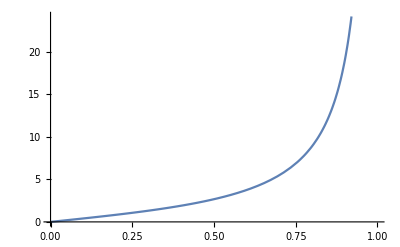

```mathematica
Plot[(4 y)/(1-y^2),{y,0,1}]
```

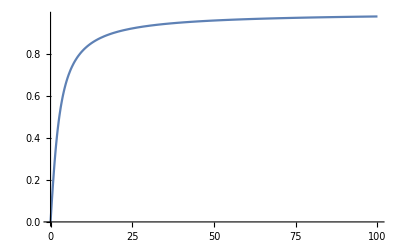

```mathematica
Plot[((8+ν^2-4 √(4+ν^2))/(8+ν^2+4 √(4+ν^2)))^(1/4),{ν,0,100},PlotRange->All]
```

```mathematica
Reduce[y==((8+ν^2-4 √(4+ν^2))/(8+ν^2+4 √(4+ν^2)))^(1/4)&&ν>0&&0<y,ν]//Simplify
```

0<y<1&&ν==-(4 y)/(-1+y^2)

```mathematica
toprightpoly[n+3]-((16+3 ν^2)toprightpoly[n+2]+(-16 ν^2-3 ν^4)  toprightpoly[n+1]+ν^6 toprightpoly[n])/.toprightpoly[n+a_]->λ^a/.toprightpoly[n]->1//Factor
```

(λ-ν^2) (-16 λ+λ^2-2 λ ν^2+ν^4)

```mathematica
Collect[-16 λ+λ^2-2 λ ν^2+ν^4,λ]
```

λ^2+ν^4+λ (-16-2 ν^2)

```mathematica
(Λ^2-ν^2)^2-16 Λ^2//Factor
```

(-4 Λ+Λ^2-ν^2) (4 Λ+Λ^2-ν^2)

```mathematica
(-y+y^(2 n)+y^(2+2 n)+y^(1+4 n))/y==0//Apart//Expand
```

```mathematica
-1+y^(4 n)+y^(-1+2 n)+y^(1+2 n)==0
```

```mathematica
y^(4 n)+y^(-1+2 n)+y^(1+2 n)==1
```

### But this is exactly the poly we had in the θ=1 notebook!

## For topleftpoly:

```mathematica
(-4 (8+ν^2-4 √(4+ν^2))^n+ν^2 (8+ν^2-4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2-4 √(4+ν^2))^n+4 (8+ν^2+4 √(4+ν^2))^n-ν^2 (8+ν^2+4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2+4 √(4+ν^2))^n)/(4 √(4+ν^2))/.n->1//Simplify
```

16-ν^2

```mathematica
(16^n (1-y^2)^(-2 n) (-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)))/((-1+y) (1+y) (1+y^2))/.n->1
```

```mathematica
(16 (-1+3 y^2-3 y^6+y^8))/((-1+y) (1+y) (1-y^2)^2 (1+y^2))//Factor
```

(16 (-1-y+y^2) (-1+y+y^2))/((-1+y)^2 (1+y)^2)

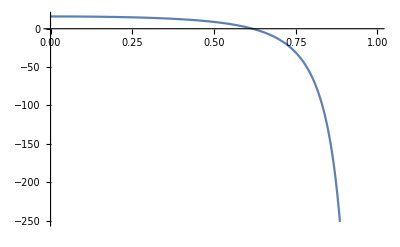

```mathematica
Plot[(16 (-1+3 y^2-3 y^6+y^8))/((-1+y) (1+y) (1-y^2)^2 (1+y^2)),{y,0,1}]
```

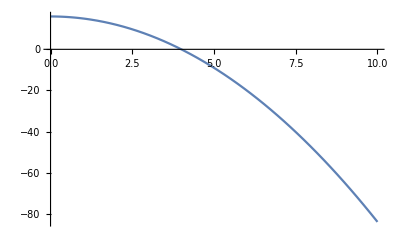

```mathematica
Plot[16-ν^2,{ν,0,10}]
```

```mathematica
16-ν^2/.ν->-(4 y)/(-1+y^2)
```

```mathematica
16-(16 y^2)/((-1+y^2)^2)//Factor
```

(16 (-1-y+y^2) (-1+y+y^2))/((-1+y)^2 (1+y)^2)

```mathematica
Reduce[-1+3 y^2-3 y^6+y^8==0&&0<y<1]//N
```

y==0.618034

```mathematica
Simplify[(-4 (8+ν^2-4 √(4+ν^2))^n+ν^2 (8+ν^2-4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2-4 √(4+ν^2))^n+4 (8+ν^2+4 √(4+ν^2))^n-ν^2 (8+ν^2+4 √(4+ν^2))^n+2 √(4+ν^2) (8+ν^2+4 √(4+ν^2))^n)/(4 √(4+ν^2))/.ν->-(4 y)/(-1+y^2),0<y<1]
```

```mathematica
(16^n (1-y^2)^(-2 n) (-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)))/(-1+y^4)//Factor
```

(16^n (1-y^2)^(-2 n) (-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)))/((-1+y) (1+y) (1+y^2))

### Now we got this poly; interestingly, it can always be factored:

```mathematica
(-1+3 y^2-3 y^(2+4 n)+y^(4+4 n))/(-1+y^4)//Apart
```

(y^(2+4 n) (-3+y^2))/((-1+y) (1+y) (1+y^2))+(-1+3 y^2)/((-1+y) (1+y) (1+y^2))

```mathematica
Table[Factor[-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)],{n,0,5}]
```

{(-1+y) (1+y) (1+y^2),(-1+y) (1+y) (1+y^2) (-1-y+y^2) (-1+y+y^2),(-1+y) (1+y) (1+y^2) (1-y-y^2-y^3+y^4) (1+y-y^2+y^3+y^4),(-1+y) (1+y) (1+y^2) (1-3 y^2+y^4-3 y^6+y^8-3 y^10+y^12),(-1+y) (1+y) (1+y^2) (1-3 y^2+y^4-3 y^6+y^8-3 y^10+y^12-3 y^14+y^16),(-1+y) (1+y) (1+y^2) (1-3 y^2+y^4-3 y^6+y^8-3 y^10+y^12-3 y^14+y^16-3 y^18+y^20)}

### After making the sign apparent:

```mathematica
(16^n (1-y^2)^(-2 n) (-(-1+3 y^2-3 y^(2+4 n)+y^(4+4 n))))/((1-y^2) (1+y^2))==(16^n (1-y^2)^(-2 n) (-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)))/((-1+y) (1+y) (1+y^2))//Simplify
```

True

### The sign of the top left and the top right entries of the matrix are the same as the signs of the following two polynomials:

```mathematica
{-(-1+3 y^2-3 y^(2+4 n)+y^(4+4 n)),-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)}//Simplify
```

{1-3 y^2+3 y^(2+4 n)-y^(4+4 n),-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)}

```mathematica
Table[{1-3 y^2+3 y^(2+4 n)-y^(4+4 n),-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)},{n,0,10}]
```

{{1-y^4,1+y^2},{1-3 y^2+3 y^6-y^8,-y+y^2+y^4+y^5},{1-3 y^2+3 y^10-y^12,-y+y^4+y^6+y^9},{1-3 y^2+3 y^14-y^16,-y+y^6+y^8+y^13},{1-3 y^2+3 y^18-y^20,-y+y^8+y^10+y^17},{1-3 y^2+3 y^22-y^24,-y+y^10+y^12+y^21},{1-3 y^2+3 y^26-y^28,-y+y^12+y^14+y^25},{1-3 y^2+3 y^30-y^32,-y+y^14+y^16+y^29},{1-3 y^2+3 y^34-y^36,-y+y^16+y^18+y^33},{1-3 y^2+3 y^38-y^40,-y+y^18+y^20+y^37},{1-3 y^2+3 y^42-y^44,-y+y^20+y^22+y^41}}

### So we need to prove that the blue and the yellow polys cannot be simultaneosly positive for any y∈(0,1):

```mathematica
Manipulate[Plot[Evaluate[{1-3 y^2+3 y^(2+4 n)-y^(4+4 n),-y+y^(2 n)+y^(2+2 n)+y^(1+4 n)}],{y,0,1},WorkingPrecision->130],{n,1,15,1}]
```

These curves are decreasing in n for any fixed 0<y<1:

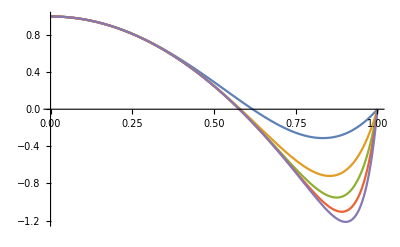

```mathematica
Plot[Evaluate@Table[1-3 y^2+3 y^(2+4 n)-y^(4+4 n),{n,1,5}],{y,0,1}]
```

```mathematica
D[1-3 y^2+3 y^(2+4 n)-y^(4+4 n),n]//Factor
```

-4 y^(2+4 n) (-3+y^2) Log[y]

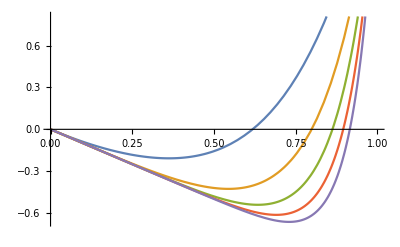

```mathematica
Plot[Evaluate@Table[-y+y^(2 n)+y^(2+2 n)+y^(1+4 n),{n,1,5}],{y,0,1}]
```

```mathematica
D[-y+y^(2 n)+y^(2+2 n)+y^(1+4 n),n]//Simplify
```

2 y^(2 n) (1+y^2+2 y^(1+2 n)) Log[y]

```mathematica
D[-y+y^(2 n)+y^(2+2 n)+y^(1+4 n),y,y]//Simplify
```

y^(2 n) (2 (1+n) (1+2 n)+(2 n (-1+2 n))/y^2+4 n (1+4 n) y^(-1+2 n))

# It seems true that for a general θ∈[0,1], entry_(1,2) and entry_(1,m) have the opposite signs for even values of the matrix size m: CLARIFY the ν vs. (-ν) ISSUE!

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Factor[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,2,8,2}]]
```

{{(4-θ ν^2+θ^2 ν^2)/(4+θ^2 ν^2),-(2 ν)/(4+θ^2 ν^2)},{(2-θ ν^2+2 θ^2 ν^2)/(2 (1+θ^2 ν^2)),ν/(2 (1+θ^2 ν^2)),(θ ν^2)/(2 (1+θ^2 ν^2)),-ν/(2 (1+θ^2 ν^2))},{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(2 ν)/(4+3 θ^2 ν^2),(θ ν^2)/(4+3 θ^2 ν^2),0,(θ ν^2)/(4+3 θ^2 ν^2),-(2 ν)/(4+3 θ^2 ν^2)},{(8-4 θ ν^2+12 θ^2 ν^2-3 θ^3 ν^4+4 θ^4 ν^4)/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),(ν (4+3 θ^2 ν^2))/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),(θ ν^2)/(4 (1+θ^2 ν^2)),(θ^2 ν^3)/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),(θ^3 ν^4)/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),-(θ^2 ν^3)/(4 (1+θ^2 ν^2) (2+θ^2 ν^2)),(θ ν^2)/(4 (1+θ^2 ν^2)),-(ν (4+3 θ^2 ν^2))/(4 (1+θ^2 ν^2) (2+θ^2 ν^2))}}

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Factor[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)][[1]],{m,3,9,2}]]
```

{{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(ν (2+θ ν))/(4+3 θ^2 ν^2),(ν (-2+θ ν))/(4+3 θ^2 ν^2)},{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)},{(64-32 θ ν^2+112 θ^2 ν^2-32 θ^3 ν^4+56 θ^4 ν^4-6 θ^5 ν^6+7 θ^6 ν^6)/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (32+32 θ^2 ν^2+6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ ν^2 (16+12 θ^2 ν^2-2 θ^3 ν^3+θ^4 ν^4))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ^2 ν^3 (8+4 θ ν+4 θ^2 ν^2+θ^3 ν^3))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ^2 ν^3 (-8+4 θ ν-4 θ^2 ν^2+θ^3 ν^3))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(θ ν^2 (16+12 θ^2 ν^2+2 θ^3 ν^3+θ^4 ν^4))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6)},{(256-128 θ ν^2+576 θ^2 ν^2-192 θ^3 ν^4+432 θ^4 ν^4-80 θ^5 ν^6+120 θ^6 ν^6-8 θ^7 ν^8+9 θ^8 ν^8)/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(ν (128+192 θ^2 ν^2+80 θ^4 ν^4+8 θ^6 ν^6+θ^7 ν^7))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ ν^2 (64+80 θ^2 ν^2+24 θ^4 ν^4-2 θ^5 ν^5+θ^6 ν^6))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ^2 ν^3 (4+θ^2 ν^2) (8+6 θ^2 ν^2+θ^3 ν^3))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ^3 ν^4 (16-8 θ ν+12 θ^2 ν^2-4 θ^3 ν^3+θ^4 ν^4))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ^3 ν^4 (16+8 θ ν+12 θ^2 ν^2+4 θ^3 ν^3+θ^4 ν^4))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ^2 ν^3 (4+θ^2 ν^2) (-8-6 θ^2 ν^2+θ^3 ν^3))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(θ ν^2 (64+80 θ^2 ν^2+24 θ^4 ν^4+2 θ^5 ν^5+θ^6 ν^6))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6)),(ν (-128-192 θ^2 ν^2-80 θ^4 ν^4-8 θ^6 ν^6+θ^7 ν^7))/((4+3 θ^2 ν^2) (64+96 θ^2 ν^2+36 θ^4 ν^4+3 θ^6 ν^6))}}

```mathematica
Union@Table[RotateLeft[({{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4)}})[[n+1]],n],{n,0,4}]
```

{{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}}

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)[[1]],{m,13,13,1}]]//Factor
```

{{-(-4096-2048 θ ν^2-9216 θ^2 ν^2-5120 θ^3 ν^4-6400 θ^4 ν^4-4608 θ^5 ν^6-768 θ^6 ν^6-1792 θ^7 ν^8+672 θ^8 ν^8-280 θ^9 ν^10+196 θ^10 ν^10-12 θ^11 ν^12+11 θ^12 ν^12)/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),((-1+2 θ) ν (-2048-5120 θ^2 ν^2-4608 θ^4 ν^4-1792 θ^6 ν^6-280 θ^8 ν^8-12 θ^10 ν^10+θ^11 ν^11))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ (-1+2 θ) ν^2 (1024+2304 θ^2 ν^2+1792 θ^4 ν^4+560 θ^6 ν^6+60 θ^8 ν^8+2 θ^9 ν^9+θ^10 ν^10))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ^2 (-1+2 θ) ν^3 (-512-1024 θ^2 ν^2-672 θ^4 ν^4-160 θ^6 ν^6+4 θ^7 ν^7-10 θ^8 ν^8+θ^9 ν^9))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ^3 (-1+2 θ) ν^4 (256+448 θ^2 ν^2+240 θ^4 ν^4+8 θ^5 ν^5+40 θ^6 ν^6+4 θ^7 ν^7+θ^8 ν^8))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ^4 (-1+2 θ) ν^5 (-128-192 θ^2 ν^2+16 θ^3 ν^3-80 θ^4 ν^4+12 θ^5 ν^5-8 θ^6 ν^6+θ^7 ν^7))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ^5 (-1+2 θ) ν^6 (64+32 θ ν+80 θ^2 ν^2+32 θ^3 ν^3+24 θ^4 ν^4+6 θ^5 ν^5+θ^6 ν^6))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ^5 (-1+2 θ) ν^6 (64-32 θ ν+80 θ^2 ν^2-32 θ^3 ν^3+24 θ^4 ν^4-6 θ^5 ν^5+θ^6 ν^6))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ^4 (-1+2 θ) ν^5 (128+192 θ^2 ν^2+16 θ^3 ν^3+80 θ^4 ν^4+12 θ^5 ν^5+8 θ^6 ν^6+θ^7 ν^7))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ^3 (-1+2 θ) ν^4 (256+448 θ^2 ν^2+240 θ^4 ν^4-8 θ^5 ν^5+40 θ^6 ν^6-4 θ^7 ν^7+θ^8 ν^8))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ^2 (-1+2 θ) ν^3 (512+1024 θ^2 ν^2+672 θ^4 ν^4+160 θ^6 ν^6+4 θ^7 ν^7+10 θ^8 ν^8+θ^9 ν^9))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),(θ (-1+2 θ) ν^2 (1024+2304 θ^2 ν^2+1792 θ^4 ν^4+560 θ^6 ν^6+60 θ^8 ν^8-2 θ^9 ν^9+θ^10 ν^10))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12),((-1+2 θ) ν (2048+5120 θ^2 ν^2+4608 θ^4 ν^4+1792 θ^6 ν^6+280 θ^8 ν^8+12 θ^10 ν^10+θ^11 ν^11))/(4096+13312 θ^2 ν^2+16640 θ^4 ν^4+9984 θ^6 ν^6+2912 θ^8 ν^8+364 θ^10 ν^10+13 θ^12 ν^12)}}

```mathematica
(1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16){(1+(3 θ^2 ν^2)/4+(θ^4 ν^4)/16)/(1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16)-((1-θ) ν (-(θ ν)/2-(θ^3 ν^3)/4+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16))+((1-θ) ν ((θ ν)/2+(θ^3 ν^3)/4+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16)),((1-θ) ν (1+(3 θ^2 ν^2)/4+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16))+(-(θ ν)/2-(θ^3 ν^3)/4+(θ^4 ν^4)/16)/(1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16)-((1-θ) ν ((θ^2 ν^2)/4+(θ^3 ν^3)/8+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16)),((1-θ) ν (-(θ ν)/2-(θ^3 ν^3)/4+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16))-((1-θ) ν ((θ^2 ν^2)/4-(θ^3 ν^3)/8+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16))+((θ^2 ν^2)/4+(θ^3 ν^3)/8+(θ^4 ν^4)/16)/(1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16),((θ^2 ν^2)/4-(θ^3 ν^3)/8+(θ^4 ν^4)/16)/(1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16)+((1-θ) ν ((θ^2 ν^2)/4+(θ^3 ν^3)/8+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16))-((1-θ) ν ((θ ν)/2+(θ^3 ν^3)/4+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16)),-((1-θ) ν (1+(3 θ^2 ν^2)/4+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16))+((1-θ) ν ((θ^2 ν^2)/4-(θ^3 ν^3)/8+(θ^4 ν^4)/16))/(2 (1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16))+((θ ν)/2+(θ^3 ν^3)/4+(θ^4 ν^4)/16)/(1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16)}//Simplify//Expand
```

{1+(θ ν^2)/2+(θ^2 ν^2)/4+(θ^3 ν^4)/4-(3 θ^4 ν^4)/16,ν/2-θ ν+(θ^2 ν^3)/4-(θ^3 ν^3)/2-(θ^3 ν^4)/16+(θ^4 ν^4)/8,-(θ ν^2)/4+(θ^2 ν^2)/2-(θ^2 ν^3)/8+(θ^3 ν^3)/4-(θ^3 ν^4)/16+(θ^4 ν^4)/8,-(θ ν^2)/4+(θ^2 ν^2)/2+(θ^2 ν^3)/8-(θ^3 ν^3)/4-(θ^3 ν^4)/16+(θ^4 ν^4)/8,-ν/2+θ ν-(θ^2 ν^3)/4+(θ^3 ν^3)/2-(θ^3 ν^4)/16+(θ^4 ν^4)/8}

```mathematica
{1+(θ ν^2)/2+(θ^2 ν^2)/4+(θ^3 ν^4)/4-(3 θ^4 ν^4)/16,ν/2-θ ν+(θ^2 ν^3)/4-(θ^3 ν^3)/2-(θ^3 ν^4)/16+(θ^4 ν^4)/8,-(θ ν^2)/4+(θ^2 ν^2)/2-(θ^2 ν^3)/8+(θ^3 ν^3)/4-(θ^3 ν^4)/16+(θ^4 ν^4)/8,-(θ ν^2)/4+(θ^2 ν^2)/2+(θ^2 ν^3)/8-(θ^3 ν^3)/4-(θ^3 ν^4)/16+(θ^4 ν^4)/8,-ν/2+θ ν-(θ^2 ν^3)/4+(θ^3 ν^3)/2-(θ^3 ν^4)/16+(θ^4 ν^4)/8}//TeXForm
```

\left\{-\frac{3}{16} \theta ^4 \nu ^4+\frac{\theta ^3 \nu ^4}{4}+\frac{\theta ^2 \nu ^2}{4}+\frac{\theta  \nu ^2}{2}+1,\frac{\theta ^4 \nu
   ^4}{8}-\frac{\theta ^3 \nu ^4}{16}-\frac{\theta ^3 \nu ^3}{2}+\frac{\theta ^2 \nu ^3}{4}-\theta  \nu +\frac{\nu }{2},\frac{\theta ^4 \nu
   ^4}{8}-\frac{\theta ^3 \nu ^4}{16}+\frac{\theta ^3 \nu ^3}{4}-\frac{\theta ^2 \nu ^3}{8}+\frac{\theta ^2 \nu ^2}{2}-\frac{\theta  \nu
   ^2}{4},\frac{\theta ^4 \nu ^4}{8}-\frac{\theta ^3 \nu ^4}{16}-\frac{\theta ^3 \nu ^3}{4}+\frac{\theta ^2 \nu ^3}{8}+\frac{\theta ^2 \nu
   ^2}{2}-\frac{\theta  \nu ^2}{4},\frac{\theta ^4 \nu ^4}{8}-\frac{\theta ^3 \nu ^4}{16}+\frac{\theta ^3 \nu ^3}{2}-\frac{\theta ^2 \nu ^3}{4}+\theta 
   \nu -\frac{\nu }{2}\right\}

```mathematica
{1+(θ ν^2)/4-(θ^2 ν^2)/4,-ν/2+θ ν}//TeXForm
```

\left\{-\frac{1}{4} \theta ^2 \nu ^2+\frac{\theta  \nu ^2}{4}+1,\theta  \nu -\frac{\nu }{2}\right\}

```mathematica
1/(1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16)//TeXForm
```

\frac{1}{\frac{5 \theta ^4 \nu ^4}{16}+\frac{5 \theta ^2 \nu ^2}{4}+1}

# General 0<θ≤1, ν>0, and size=odd=m=2k+1; the 1st row of the matrix, multiplied by the determinant (which we already established to be positive)

### Note! In our earlier file central_scheme_positivity.nb, we used a different parametrization: ν here is (–2ν) there. Reason: advection equation rearranged to the other side; the coefficients 1/2 combined into ν – this time we follow a different convention. So in the earlier file the critical matrix element governing non-negativity was at position (1,2), now we have a different position.

```mathematica
Table[((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand,{m,3,9,2}]
```

{1+(3 θ^2 ν^2)/4,1+(5 θ^2 ν^2)/4+(5 θ^4 ν^4)/16,1+(7 θ^2 ν^2)/4+(7 θ^4 ν^4)/8+(7 θ^6 ν^6)/64,1+(9 θ^2 ν^2)/4+(27 θ^4 ν^4)/16+(15 θ^6 ν^6)/32+(9 θ^8 ν^8)/256}

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]]//Simplify//Expand,{m,3,9,2}]]
```

```mathematica
{{1-(θ ν^2)/2+(3 θ^2 ν^2)/4,ν/2+(θ ν^2)/4,-ν/2+(θ ν^2)/4},{1-(θ ν^2)/2+(5 θ^2 ν^2)/4-(θ^3 ν^4)/4+(5 θ^4 ν^4)/16,ν/2+(θ^2 ν^3)/4+(θ^3 ν^4)/16,(θ ν^2)/4-(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ ν^2)/4+(θ^2 ν^3)/8+(θ^3 ν^4)/16,-ν/2-(θ^2 ν^3)/4+(θ^3 ν^4)/16},{1-(θ ν^2)/2+(7 θ^2 ν^2)/4-(θ^3 ν^4)/2+(7 θ^4 ν^4)/8-(3 θ^5 ν^6)/32+(7 θ^6 ν^6)/64,ν/2+(θ^2 ν^3)/2+(3 θ^4 ν^5)/32+(θ^5 ν^6)/64,(θ ν^2)/4+(3 θ^3 ν^4)/16-(θ^4 ν^5)/32+(θ^5 ν^6)/64,(θ^2 ν^3)/8+(θ^3 ν^4)/16+(θ^4 ν^5)/16+(θ^5 ν^6)/64,-1/8 θ^2 ν^3+(θ^3 ν^4)/16-(θ^4 ν^5)/16+(θ^5 ν^6)/64,(θ ν^2)/4+(3 θ^3 ν^4)/16+(θ^4 ν^5)/32+(θ^5 ν^6)/64,-ν/2-(θ^2 ν^3)/2-(3 θ^4 ν^5)/32+(θ^5 ν^6)/64},{1-(θ ν^2)/2+(9 θ^2 ν^2)/4-(3 θ^3 ν^4)/4+(27 θ^4 ν^4)/16-(5 θ^5 ν^6)/16+(15 θ^6 ν^6)/32-(θ^7 ν^8)/32+(9 θ^8 ν^8)/256,ν/2+(3 θ^2 ν^3)/4+(5 θ^4 ν^5)/16+(θ^6 ν^7)/32+(θ^7 ν^8)/256,(θ ν^2)/4+(5 θ^3 ν^4)/16+(3 θ^5 ν^6)/32-(θ^6 ν^7)/128+(θ^7 ν^8)/256,(θ^2 ν^3)/8+(θ^4 ν^5)/8+(θ^5 ν^6)/64+(3 θ^6 ν^7)/128+(θ^7 ν^8)/256,(θ^3 ν^4)/16-(θ^4 ν^5)/32+(3 θ^5 ν^6)/64-(θ^6 ν^7)/64+(θ^7 ν^8)/256,(θ^3 ν^4)/16+(θ^4 ν^5)/32+(3 θ^5 ν^6)/64+(θ^6 ν^7)/64+(θ^7 ν^8)/256,-1/8 θ^2 ν^3-(θ^4 ν^5)/8+(θ^5 ν^6)/64-(3 θ^6 ν^7)/128+(θ^7 ν^8)/256,(θ ν^2)/4+(5 θ^3 ν^4)/16+(3 θ^5 ν^6)/32+(θ^6 ν^7)/128+(θ^7 ν^8)/256,-ν/2-(3 θ^2 ν^3)/4-(5 θ^4 ν^5)/16-(θ^6 ν^7)/32+(θ^7 ν^8)/256}}
```

### It seems that the top left elements satisfy a second-order recursion, while all the others in the 1st row satistfy the SAME 3rd-order recursion as a function of the odd matirx size

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,1]]//Simplify//Expand,{m,3,11,2}]]
```

{1+(θ^2 ν^2)/2,-1/16 θ^4 ν^4}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,2]]//Simplify//Expand,{m,3,15,2}]]
```

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,3]]//Simplify//Expand,{m,3,15,2}]]
```

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,4]]//Simplify//Expand,{m,5,17,2}]]
```

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,5]]//Simplify//Expand,{m,5,17,2}]]
```

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
Expand@FindLinearRecurrence@With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,6]]//Simplify//Expand,{m,7,19,2}]]
```

### Examining the characteristic polynomials of the obtained recursions

{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}

```mathematica
λ^3-((1+(3 μ)/4)λ^2+(-1/4 μ-(3 μ^2)/16)λ+(μ^3/64))/.λ->κ
```

```mathematica
κ^3-κ^2 (1+(3 μ)/4)-μ^3/64-κ (-μ/4-(3 μ^2)/16)//TeXForm
```

\kappa ^3-\kappa ^2 \left(\frac{3 \mu }{4}+1\right)-\kappa  \left(-\frac{3 \mu ^2}{16}-\frac{\mu }{4}\right)-\frac{\mu ^3}{64}

```mathematica
κ^3-κ^2 (1+(3 μ)/4)-μ^3/64-κ (-μ/4-(3 μ^2)/16)//Factor
```

```mathematica
(κ-μ/4) (κ^2+μ^2/16-1/2 κ (2+μ))
```

```mathematica
λ^3-((1+(3 θ^2 ν^2)/4)λ^2+(-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16)λ+((θ^6 ν^6)/64))//Factor
```

1/64 (4 λ-θ^2 ν^2) (-16 λ+16 λ^2-8 θ^2 λ ν^2+θ^4 ν^4)

```mathematica
{1+(θ^2 ν^2)/2,-1/16 θ^4 ν^4}
```

```mathematica
λ^2-((1+(θ^2 ν^2)/2)λ+(-1/16 θ^4 ν^4))//Factor
```

1/16 (-16 λ+16 λ^2-8 θ^2 λ ν^2+θ^4 ν^4)

```mathematica
Solve[κ^2-κ (1+μ/2)+μ^2/16==0,κ]
```

{{κ→1/4 (2+μ-2 √(1+μ))},{κ→1/4 (2+μ+2 √(1+μ))}}

```mathematica
1/4 (2+μ+2 √(1+μ))//TeXForm
```

\frac{1}{4} \left(\mu +2 \sqrt{\mu +1}+2\right)

```mathematica
λ^2-((1+μ/2)λ+(-1/16 μ^2))/.λ->κ
```

```mathematica
κ^2-κ (1+μ/2)+μ^2/16//TeXForm
```

\kappa ^2-\kappa  \left(\frac{\mu }{2}+1\right)+\frac{\mu ^2}{16}

### Two observations: 1. the new variable μ=(ν θ)^2 seems to be advatageous (we used the same variable when dealing with the determinants!) 2. the char. poly of the 3rd-order recursion contains that of the 2nd-order one as a factor Remark: matrix size=2k+1

### The explicit form of the top left element:

```mathematica
RSolve[{topleftelement[k+2]== (1+μ/2)topleftelement[k+1]-1/16 μ^2  topleftelement[k],topleftelement[1]==1-μ/(2θ)+(3 μ)/4,topleftelement[2]==1-μ/(2θ)+(5 μ)/4-μ^2/(4θ)+(5 μ^2)/16},topleftelement[k],k]//Expand
```

{{topleftelement[k]→2^(-1-2 k) (2+μ-2 √(1+μ))^k-(2^(-1-2 k) (2+μ-2 √(1+μ))^k)/(√(1+μ))-(2^(-1-2 k) μ (2+μ-2 √(1+μ))^k)/(√(1+μ))+(2^(-1-2 k) μ (2+μ-2 √(1+μ))^k)/(θ √(1+μ))+2^(-1-2 k) (2+μ+2 √(1+μ))^k+(2^(-1-2 k) (2+μ+2 √(1+μ))^k)/(√(1+μ))+(2^(-1-2 k) μ (2+μ+2 √(1+μ))^k)/(√(1+μ))-(2^(-1-2 k) μ (2+μ+2 √(1+μ))^k)/(θ √(1+μ))}}

### We apply a non-linear change of variables: μ== (4 y^2)/((1-y^2)^2)∈(0,+∞) ⧦ y==(√(1+μ)-1)/(√μ)==(√(1+(θ ν)^2)-1)/(θ ν)∈(0,1), with μ==(θ ν)^2 Reason: this way μ y^2==2+μ-2 √(1+μ) and μ/y^2==2+μ+2 √(1+μ)

```mathematica
μ ((√(1+μ)-1)/(√μ))^2//Expand//Together
```

2+μ-2 √(1+μ)

```mathematica
μ/((√(1+μ)-1)/(√μ))^2==2+μ+2 √(1+μ)//Simplify
```

True

```mathematica
Reduce[μ== (4 y^2)/((1-y^2)^2)&&μ>0&&0<y<1,y]
```

μ>0&&y==Root[μ+(-4-2 μ) #1^2+μ #1^4&,3]

### ToRadicals here selects the wrong root!

```mathematica
Root[μ+(-4-2 μ) #1^2+μ #1^4&,3]//ToRadicals
```

√(1+2/μ+(2 √(1+μ))/μ)

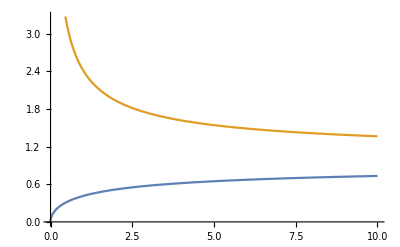

```mathematica
Plot[{Root[μ+(-4-2 μ) #1^2+μ #1^4&,3],√(1+2/μ+(2 √(1+μ))/μ)},{μ,0,10}]
```

that is

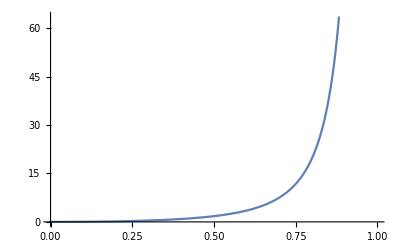

```mathematica
Plot[(4 y^2)/((1-y^2)^2),{y,0,1}]
```

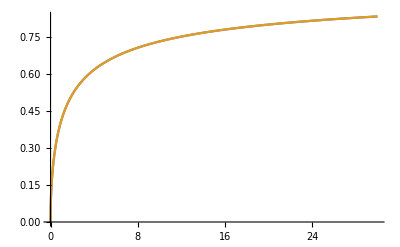

```mathematica
Plot[{(√(1+μ)-1)/(√μ),Root[μ+(-4-2 μ) #1^2+μ #1^4&,3]},{μ,0,30},PlotRange->All]
```

```mathematica
Simplify[2^(-1-2 k) (2+μ-2 √(1+μ))^k-(2^(-1-2 k) (2+μ-2 √(1+μ))^k)/(√(1+μ))-(2^(-1-2 k) μ (2+μ-2 √(1+μ))^k)/(√(1+μ))+(2^(-1-2 k) μ (2+μ-2 √(1+μ))^k)/(θ √(1+μ))+2^(-1-2 k) (2+μ+2 √(1+μ))^k+(2^(-1-2 k) (2+μ+2 √(1+μ))^k)/(√(1+μ))+(2^(-1-2 k) μ (2+μ+2 √(1+μ))^k)/(√(1+μ))-(2^(-1-2 k) μ (2+μ+2 √(1+μ))^k)/(θ √(1+μ))/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ)

```mathematica
FullSimplify[((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ)/.y->(√(1+μ)-1)/(√μ)/.μ->(ν θ)^2,ν>0&&0<θ≤1&&k∈Integers]
```

((θ ν)^(4 k) (2-2 √(1+θ^2 ν^2))^(-2 k) (-θ-((-2+θ) (-1+√(1+θ^2 ν^2))^2)/(θ^2 ν^2)+θ ((-1+√(1+θ^2 ν^2))/(θ ν))^(4 (1+k))+(-2+θ) ((-1+√(1+θ^2 ν^2))/(θ ν))^(2+4 k)))/(θ (-1+((-1+√(1+θ^2 ν^2))^4)/(θ^4 ν^4)))

```mathematica
Expand@FullSimplify[Table[((θ ν)^(4 k) (2-2 √(1+θ^2 ν^2))^(-2 k) (-θ-((-2+θ) (-1+√(1+θ^2 ν^2))^2)/(θ^2 ν^2)+θ ((-1+√(1+θ^2 ν^2))/(θ ν))^(4 (1+k))+(-2+θ) ((-1+√(1+θ^2 ν^2))/(θ ν))^(2+4 k)))/(θ (-1+((-1+√(1+θ^2 ν^2))^4)/(θ^4 ν^4))),{k,1,6}],ν>0&&0<θ≤1&&k∈Integers]
```

{1-(θ ν^2)/2+(3 θ^2 ν^2)/4,1-(θ ν^2)/2+(5 θ^2 ν^2)/4-(θ^3 ν^4)/4+(5 θ^4 ν^4)/16,1-(θ ν^2)/2+(7 θ^2 ν^2)/4-(θ^3 ν^4)/2+(7 θ^4 ν^4)/8-(3 θ^5 ν^6)/32+(7 θ^6 ν^6)/64,1-(θ ν^2)/2+(9 θ^2 ν^2)/4-(3 θ^3 ν^4)/4+(27 θ^4 ν^4)/16-(5 θ^5 ν^6)/16+(15 θ^6 ν^6)/32-(θ^7 ν^8)/32+(9 θ^8 ν^8)/256,1-(θ ν^2)/2+(11 θ^2 ν^2)/4-θ^3 ν^4+(11 θ^4 ν^4)/4-(21 θ^5 ν^6)/32+(77 θ^6 ν^6)/64-(5 θ^7 ν^8)/32+(55 θ^8 ν^8)/256-(5 θ^9 ν^10)/512+(11 θ^10 ν^10)/1024,1-(θ ν^2)/2+(13 θ^2 ν^2)/4-(5 θ^3 ν^4)/4+(65 θ^4 ν^4)/16-(9 θ^5 ν^6)/8+(39 θ^6 ν^6)/16-(7 θ^7 ν^8)/16+(91 θ^8 ν^8)/128-(35 θ^9 ν^10)/512+(91 θ^10 ν^10)/1024-(3 θ^11 ν^12)/1024+(13 θ^12 ν^12)/4096}

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,1]]//Simplify//Expand,{m,3,13,2}]]
```

{1-(θ ν^2)/2+(3 θ^2 ν^2)/4,1-(θ ν^2)/2+(5 θ^2 ν^2)/4-(θ^3 ν^4)/4+(5 θ^4 ν^4)/16,1-(θ ν^2)/2+(7 θ^2 ν^2)/4-(θ^3 ν^4)/2+(7 θ^4 ν^4)/8-(3 θ^5 ν^6)/32+(7 θ^6 ν^6)/64,1-(θ ν^2)/2+(9 θ^2 ν^2)/4-(3 θ^3 ν^4)/4+(27 θ^4 ν^4)/16-(5 θ^5 ν^6)/16+(15 θ^6 ν^6)/32-(θ^7 ν^8)/32+(9 θ^8 ν^8)/256,1-(θ ν^2)/2+(11 θ^2 ν^2)/4-θ^3 ν^4+(11 θ^4 ν^4)/4-(21 θ^5 ν^6)/32+(77 θ^6 ν^6)/64-(5 θ^7 ν^8)/32+(55 θ^8 ν^8)/256-(5 θ^9 ν^10)/512+(11 θ^10 ν^10)/1024,1-(θ ν^2)/2+(13 θ^2 ν^2)/4-(5 θ^3 ν^4)/4+(65 θ^4 ν^4)/16-(9 θ^5 ν^6)/8+(39 θ^6 ν^6)/16-(7 θ^7 ν^8)/16+(91 θ^8 ν^8)/128-(35 θ^9 ν^10)/512+(91 θ^10 ν^10)/1024-(3 θ^11 ν^12)/1024+(13 θ^12 ν^12)/4096}

```mathematica
With[{θ=2/3},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,1]]//Simplify//Expand,{m,3,13,2}]]
```

{1,1+(2 ν^2)/9-ν^4/81,1+(4 ν^2)/9+(2 ν^4)/81-(2 ν^6)/729,1+(2 ν^2)/3+ν^4/9-ν^8/2187,1+(8 ν^2)/9+(20 ν^4)/81+(14 ν^6)/729-(5 ν^8)/6561-(4 ν^10)/59049,1+(10 ν^2)/9+(35 ν^4)/81+(16 ν^6)/243+(14 ν^8)/6561-(14 ν^10)/59049-(5 ν^12)/531441}

```mathematica
Reduce[#&&ν>0]&/@({1,1+(2 ν^2)/9-ν^4/81,1+(4 ν^2)/9+(2 ν^4)/81-(2 ν^6)/729,1+(2 ν^2)/3+ν^4/9-ν^8/2187,1+(8 ν^2)/9+(20 ν^4)/81+(14 ν^6)/729-(5 ν^8)/6561-(4 ν^10)/59049,1+(10 ν^2)/9+(35 ν^4)/81+(16 ν^6)/243+(14 ν^8)/6561-(14 ν^10)/59049-(5 ν^12)/531441}≥0//Thread)
```

{ν>0,0<ν≤Root[-81-18 #1^2+#1^4&,2],0<ν≤Root[-729-324 #1^2-18 #1^4+2 #1^6&,2],0<ν≤Root[-2187-1458 #1^2-243 #1^4+#1^8&,2],0<ν≤Root[-59049-52488 #1^2-14580 #1^4-1134 #1^6+45 #1^8+4 #1^10&,2],0<ν≤Root[-531441-590490 #1^2-229635 #1^4-34992 #1^6-1134 #1^8+126 #1^10+5 #1^12&,2]}

```mathematica
{ν>0,0<ν≤Root[-81-18 #1^2+#1^4&,2],0<ν≤Root[-729-324 #1^2-18 #1^4+2 #1^6&,2],0<ν≤Root[-2187-1458 #1^2-243 #1^4+#1^8&,2],0<ν≤Root[-59049-52488 #1^2-14580 #1^4-1134 #1^6+45 #1^8+4 #1^10&,2],0<ν≤Root[-531441-590490 #1^2-229635 #1^4-34992 #1^6-1134 #1^8+126 #1^10+5 #1^12&,2]}//N
```

{ν>0.,0.<ν≤4.66132,0.<ν≤4.32475,0.<ν≤4.26183,0.<ν≤4.24734,0.<ν≤4.24381}

### so the sign of the top left element is detemined by the sign of ((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ), which is

y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ

```mathematica
((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ)
```

```mathematica
((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ)//TeXForm
```

\frac{\left(y^2-1\right)^{-2 k} \left(-\theta +(\theta -2) y^{4 k+2}+\theta  y^{4 k+4}-(\theta -2) y^2\right)}{\theta  \left(y^4-1\right)}

```mathematica
Table[Reduce[(0≤y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->2/3)&&0<y<1],{k,1,6}]
```

{0<y<1,0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16-2 #1^18+#1^20&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16-2 #1^18+#1^20-2 #1^22+#1^24&,3]}

```mathematica
Reduce[#&&ν>0]&/@({0<y<1,0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16-2 #1^18+#1^20&,3],0<y≤Root[1-2 #1^2+#1^4-2 #1^6+#1^8-2 #1^10+#1^12-2 #1^14+#1^16-2 #1^18+#1^20-2 #1^22+#1^24&,3]}/.y->(√(1+μ)-1)/(√μ)/.μ->(θ ν)^2/.θ->2/3)//RootReduce
```

```mathematica
{ν>0,0<ν≤Root[-81-18 #1^2+#1^4&,2],0<ν≤Root[-729-324 #1^2-18 #1^4+2 #1^6&,2],0<ν≤Root[-2187-1458 #1^2-243 #1^4+#1^8&,2],0<ν≤Root[-59049-52488 #1^2-14580 #1^4-1134 #1^6+45 #1^8+4 #1^10&,2],0<ν≤Root[-531441-590490 #1^2-229635 #1^4-34992 #1^6-1134 #1^8+126 #1^10+5 #1^12&,2]}//N
```

{ν>0.,0.<ν≤4.66132,0.<ν≤4.32475,0.<ν≤4.26183,0.<ν≤4.24734,0.<ν≤4.24381}

### The explicit form of the element_(1,2):

The initial conditions:

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,2]]//Simplify//Expand,{m,3,13,2}]]
```

{ν/2+(θ ν^2)/4,ν/2+(θ^2 ν^3)/4+(θ^3 ν^4)/16,ν/2+(θ^2 ν^3)/2+(3 θ^4 ν^5)/32+(θ^5 ν^6)/64,ν/2+(3 θ^2 ν^3)/4+(5 θ^4 ν^5)/16+(θ^6 ν^7)/32+(θ^7 ν^8)/256,ν/2+θ^2 ν^3+(21 θ^4 ν^5)/32+(5 θ^6 ν^7)/32+(5 θ^8 ν^9)/512+(θ^9 ν^10)/1024,ν/2+(5 θ^2 ν^3)/4+(9 θ^4 ν^5)/8+(7 θ^6 ν^7)/16+(35 θ^8 ν^9)/512+(3 θ^10 ν^11)/1024+(θ^11 ν^12)/4096}

```mathematica
{ν/2+(θ ν^2)/4,ν/2+(θ^2 ν^3)/4+(θ^3 ν^4)/16,ν/2+(θ^2 ν^3)/2+(3 θ^4 ν^5)/32+(θ^5 ν^6)/64}/.θ->(√μ)/ν
```

{ν/2+(√μ ν)/4,ν/2+(μ ν)/4+1/16 μ^(3/2) ν,ν/2+(μ ν)/2+(3 μ^2 ν)/32+1/64 μ^(5/2) ν}

The recursion coefficients obtained above:

```mathematica
{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}/.ν->(√μ)/θ
```

{1+(3 μ)/4,-μ/4-(3 μ^2)/16,μ^3/64}

The recursion:

```mathematica
RSolve[{secondelement[k+3]== (1+(3 μ)/4)secondelement[k+2]+(-μ/4-(3 μ^2)/16)secondelement[k+1]+μ^3/64 secondelement[k],secondelement[1]==ν/2+(√μ ν)/4,secondelement[2]==ν/2+(μ ν)/4+1/16 μ^(3/2) ν,secondelement[3]==ν/2+(μ ν)/2+(3 μ^2 ν)/32+1/64 μ^(5/2) ν},secondelement[k],k]//Expand
```

{{secondelement[k]→2^(-2 k) μ^(-1/2+k) ν-(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√(1+μ))+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√(1+μ))}}

```mathematica
Simplify[2^(-2 k) μ^(-1/2+k) ν-(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√(1+μ))+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√(1+μ))/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

-((-1+y^2)^(1-2 k) (y+y^(2 k)+y^(2+2 k)-y^(1+4 k)) ν)/(2 (y+y^3))

### Its sign is determined:

```mathematica
y+y^(2 k)+y^(2+2 k)-y^(1+4 k)
```

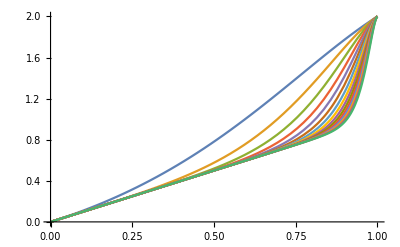

```mathematica
Plot[Evaluate@Table[y+y^(2 k)+y^(2+2 k)-y^(1+4 k),{k,1,15}],{y,0,1}]
```

```mathematica
y^(2+2 k)(1-y^(1+4 k-2k-2))
```

y^(2+2 k) (1-y^(-1+2 k))

which is trivially positive for 0<y<1.

### The explicit form of the element_(1,3):

The initial conditions:

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,3]]//Simplify//Expand,{m,3,7,2}]]
```

{-ν/2+(θ ν^2)/4,(θ ν^2)/4-(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ ν^2)/4+(3 θ^3 ν^4)/16-(θ^4 ν^5)/32+(θ^5 ν^6)/64}

```mathematica
{-ν/2+(θ ν^2)/4,(θ ν^2)/4-(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ ν^2)/4+(3 θ^3 ν^4)/16-(θ^4 ν^5)/32+(θ^5 ν^6)/64}/.θ->(√μ)/ν
```

{-ν/2+(√μ ν)/4,(√μ ν)/4-(μ ν)/8+1/16 μ^(3/2) ν,(√μ ν)/4+3/16 μ^(3/2) ν-(μ^2 ν)/32+1/64 μ^(5/2) ν}

The recursion coefficients obtained above:

```mathematica
{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}/.ν->(√μ)/θ
```

{1+(3 μ)/4,-μ/4-(3 μ^2)/16,μ^3/64}

The recursion:

```mathematica
RSolve[{thirdelement[k+3]== (1+(3 μ)/4)thirdelement[k+2]+(-μ/4-(3 μ^2)/16)thirdelement[k+1]+μ^3/64 thirdelement[k],thirdelement[1]==-ν/2+(√μ ν)/4,thirdelement[2]==(√μ ν)/4-(μ ν)/8+1/16 μ^(3/2) ν,thirdelement[3]==(√μ ν)/4+3/16 μ^(3/2) ν-(μ^2 ν)/32+1/64 μ^(5/2) ν},thirdelement[k],k]//Expand
```

{{thirdelement[k]→-2^(1-2 k) μ^(-1+k) ν+(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√μ)+(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√μ √(1+μ))+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√μ)-(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√μ √(1+μ))}}

```mathematica
Simplify[-2^(1-2 k) μ^(-1+k) ν+(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√μ)+(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√μ √(1+μ))+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√μ)-(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√μ √(1+μ))/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

-((-1+y^2)^(1-2 k) (y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k)) ν)/(2 y^2 (1+y^2))

### Its sign is determined:

```mathematica
y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k)
```

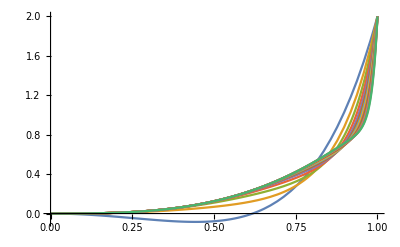

```mathematica
Plot[Evaluate@Table[y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k),{k,1,15}],{y,0,1},PlotRange->All]
```

which is trivially positive for k>1 and 0<y<1.

### The explicit form of the element_(1,4):

The initial conditions: now the matrix size is at least 5

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1,4]]//Simplify//Expand,{m,5,9,2}]]
```

{(θ ν^2)/4+(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ^2 ν^3)/8+(θ^3 ν^4)/16+(θ^4 ν^5)/16+(θ^5 ν^6)/64,(θ^2 ν^3)/8+(θ^4 ν^5)/8+(θ^5 ν^6)/64+(3 θ^6 ν^7)/128+(θ^7 ν^8)/256}

```mathematica
{(θ ν^2)/4+(θ^2 ν^3)/8+(θ^3 ν^4)/16,(θ^2 ν^3)/8+(θ^3 ν^4)/16+(θ^4 ν^5)/16+(θ^5 ν^6)/64,(θ^2 ν^3)/8+(θ^4 ν^5)/8+(θ^5 ν^6)/64+(3 θ^6 ν^7)/128+(θ^7 ν^8)/256}/.θ->(√μ)/ν
```

{(√μ ν)/4+(μ ν)/8+1/16 μ^(3/2) ν,(μ ν)/8+1/16 μ^(3/2) ν+(μ^2 ν)/16+1/64 μ^(5/2) ν,(μ ν)/8+(μ^2 ν)/8+1/64 μ^(5/2) ν+(3 μ^3 ν)/128+1/256 μ^(7/2) ν}

The recursion coefficients obtained above:

```mathematica
{1+(3 θ^2 ν^2)/4,-1/4 θ^2 ν^2-(3 θ^4 ν^4)/16,(θ^6 ν^6)/64}/.ν->(√μ)/θ
```

{1+(3 μ)/4,-μ/4-(3 μ^2)/16,μ^3/64}

The recursion: [NOTE: as for the starting index we need k≥2 to make the matrix size at least 5]

```mathematica
RSolve[{fourthelement[k+3]== (1+(3 μ)/4)fourthelement[k+2]+(-μ/4-(3 μ^2)/16)fourthelement[k+1]+μ^3/64 fourthelement[k],fourthelement[2]==(√μ ν)/4+(μ ν)/8+1/16 μ^(3/2) ν,fourthelement[3]==(μ ν)/8+1/16 μ^(3/2) ν+(μ^2 ν)/16+1/64 μ^(5/2) ν,fourthelement[4]==(μ ν)/8+(μ^2 ν)/8+1/64 μ^(5/2) ν+(3 μ^3 ν)/128+1/256 μ^(7/2) ν},fourthelement[k],k]//Expand
```

{{fourthelement[k]→2^(2-2 k) μ^(-3/2+k) ν+2^(-2 k) μ^(-1/2+k) ν-(2^(-2 k) (2+μ-2 √(1+μ))^k ν)/μ-(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√(1+μ))-(2^(-2 k) (2+μ-2 √(1+μ))^k ν)/(μ √(1+μ))-(2^(-2 k) (2+μ+2 √(1+μ))^k ν)/μ+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√(1+μ))+(2^(-2 k) (2+μ+2 √(1+μ))^k ν)/(μ √(1+μ))}}

```mathematica
Simplify[2^(2-2 k) μ^(-3/2+k) ν+2^(-2 k) μ^(-1/2+k) ν-(2^(-2 k) (2+μ-2 √(1+μ))^k ν)/μ-(2^(-1-2 k) (2+μ-2 √(1+μ))^k ν)/(√(1+μ))-(2^(-2 k) (2+μ-2 √(1+μ))^k ν)/(μ √(1+μ))-(2^(-2 k) (2+μ+2 √(1+μ))^k ν)/μ+(2^(-1-2 k) (2+μ+2 √(1+μ))^k ν)/(√(1+μ))+(2^(-2 k) (2+μ+2 √(1+μ))^k ν)/(μ √(1+μ))/.μ-> (4 y^2)/((1-y^2)^2),0<y<1&&k∈Integers]
```

-((-1+y^2)^(1-2 k) (y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k)) ν)/(2 y^3 (1+y^2))

### Its sign is determined:

```mathematica
y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k)
```

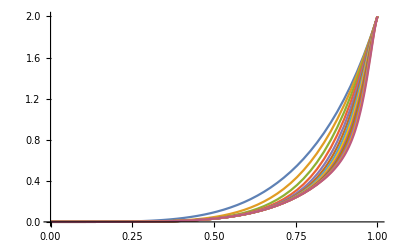

```mathematica
Plot[Evaluate@Table[y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k),{k,2,15}],{y,0,1},PlotRange->All]
```

```mathematica
Reduce[6+2k<1+4k]
```

k>5/2

which is trivially positive for k>2 and 0<y<1. For k=2:

```mathematica
y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k)/.k->2
```

y^4+y^5-y^9+y^10

### The consecutive elements in the 1st row (1st, 2nd, 3rd, 4th):

```mathematica
{((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^4) θ),-((-1+y^2)^(1-2 k) (y+y^(2 k)+y^(2+2 k)-y^(1+4 k)) ν)/(2 (y+y^3)),-((-1+y^2)^(1-2 k) (y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k)) ν)/(2 y^2 (1+y^2)),-((-1+y^2)^(1-2 k) (y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k)) ν)/(2 y^3 (1+y^2))}
```

After some transformations:

```mathematica
{((-1+y^2)^(-2 k) (-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ))/((-1+y^2) (1+y^2) θ),((1-y^2)^(1-2 k)  ν)/(2 (y+y^3))(y+y^(2 k)+y^(2+2 k)-y^(1+4 k)),((1-y^2)^(1-2 k)  ν)/(2 y^2 (1+y^2))(y^3-y^(2 k)+y^(4+2 k)+y^(1+4 k)),((1-y^2)^(1-2 k)  ν)/(2 y^3 (1+y^2))(y^5+y^(2 k)+y^(6+2 k)-y^(1+4 k))}
```

```mathematica
{((1-y^2)^(-1-2 k)(y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ))/((1+y^2) θ),((1-y^2)^(1-2 k) (1+y^(-1+2 k)+y^(1+2 k)-y^(4 k)) ν)/(2 (1+y^2)),((1-y^2)^(1-2 k) (y-y^(-2+2 k)+y^(2+2 k)+y^(-1+4 k)) ν)/(2  (1+y^2)),((1-y^2)^(1-2 k) (y^2+y^(-3+2 k)+y^(3+2 k)-y^(-2+4 k)) ν)/(2 (1+y^2))}
```

### So from this we conjecture the general structure: with y==(√(1+(θ ν)^2)-1)/(θ ν), ν>0, 0<θ≤1, matrix size m x m with m==2k+1, k≥1 we have element_(1,1) multiplied by the determinant is

```mathematica
((1-y^2)^(-1-2 k))/((1+y^2) θ)(y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ)
```

### element_(1,L) multiplied by the determinant with 2≤L≤2k+1 is

```mathematica
((1-y^2)^(1-2 k)  ν)/(2 (1+y^2))(y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)))
```

### Remark: the sign is determined by just 1 parameter, y.

### Checking these formulae by comparing the 1st row of Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)

```mathematica
Expand@FullSimplify[With[{k=7},Flatten[{((1-y^2)^(-1-2 k))/((1+y^2) θ)(y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ),Table[((1-y^2)^(1-2 k)  ν)/(2 (1+y^2))(y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))),{L,2,2k+1}]}]/.y->(-1+√(1+θ^2 ν^2))/(θ ν)],0<θ≤1&&0<ν]
```

{-16384/((-1+√(1+θ^2 ν^2))^15)+(8192 θ ν^2)/((-1+√(1+θ^2 ν^2))^15)-(122880 θ^2 ν^2)/((-1+√(1+θ^2 ν^2))^15)+(55296 θ^3 ν^4)/((-1+√(1+θ^2 ν^2))^15)-(414720 θ^4 ν^4)/((-1+√(1+θ^2 ν^2))^15)+(166400 θ^5 ν^6)/((-1+√(1+θ^2 ν^2))^15)-(832000 θ^6 ν^6)/((-1+√(1+θ^2 ν^2))^15)+(294400 θ^7 ν^8)/((-1+√(1+θ^2 ν^2))^15)-(1104000 θ^8 ν^8)/((-1+√(1+θ^2 ν^2))^15)+(340032 θ^9 ν^10)/((-1+√(1+θ^2 ν^2))^15)-(1020096 θ^10 ν^10)/((-1+√(1+θ^2 ν^2))^15)+(269192 θ^11 ν^12)/((-1+√(1+θ^2 ν^2))^15)-(672980 θ^12 ν^12)/((-1+√(1+θ^2 ν^2))^15)+(149226 θ^13 ν^14)/((-1+√(1+θ^2 ν^2))^15)-(319770 θ^14 ν^14)/((-1+√(1+θ^2 ν^2))^15)+(58140 θ^15 ν^16)/((-1+√(1+θ^2 ν^2))^15)-(218025 θ^16 ν^16)/(2 (-1+√(1+θ^2 ν^2))^15)+(62985 θ^17 ν^18)/(4 (-1+√(1+θ^2 ν^2))^15)-(104975 θ^18 ν^18)/(4 (-1+√(1+θ^2 ν^2))^15)+(46189 θ^19 ν^20)/(16 (-1+√(1+θ^2 ν^2))^15)-(138567 θ^20 ν^20)/(32 (-1+√(1+θ^2 ν^2))^15)+(21879 θ^21 ν^22)/(64 (-1+√(1+θ^2 ν^2))^15)-(29835 θ^22 ν^22)/(64 (-1+√(1+θ^2 ν^2))^15)+(1547 θ^23 ν^24)/(64 (-1+√(1+θ^2 ν^2))^15)-(7735 θ^24 ν^24)/(256 (-1+√(1+θ^2 ν^2))^15)+(455 θ^25 ν^26)/(512 (-1+√(1+θ^2 ν^2))^15)-(525 θ^26 ν^26)/(512 (-1+√(1+θ^2 ν^2))^15)+(105 θ^27 ν^28)/(8192 (-1+√(1+θ^2 ν^2))^15)-(225 θ^28 ν^28)/(16384 (-1+√(1+θ^2 ν^2))^15)-1/(65536 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)+1/(32768 θ √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)-1/(65536 θ^2 ν^2 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)-(θ^27 ν^28)/(16384 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)+(θ^28 ν^28)/(32768 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)-(θ^29 ν^30)/(32768 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)+(θ^30 ν^30)/(32768 √(1+θ^2 ν^2) (-1+√(1+θ^2 ν^2))^15)+(16384 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(√(1+θ^2 ν^2))/(32768 θ (-1+√(1+θ^2 ν^2))^15)+(√(1+θ^2 ν^2))/(65536 θ^2 ν^2 (-1+√(1+θ^2 ν^2))^15)-(268435455 θ ν^2 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(114688 θ^2 ν^2 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(1677721601 θ^3 ν^4 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(359424 θ^4 ν^4 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(4647288831 θ^5 ν^6 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(665600 θ^6 ν^6 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(7516192769 θ^7 ν^8 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(809600 θ^8 ν^8 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(7870611455 θ^9 ν^10 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(680064 θ^10 ν^10 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(5592842241 θ^11 ν^12 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(403788 θ^12 ν^12 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(2748645375 θ^13 ν^14 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(170544 θ^14 ν^14 √(1+θ^2 ν^2))/((-1+√(1+θ^2 ν^2))^15)-(934608897 θ^15 ν^16 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(101745 θ^16 ν^16 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^15)-(216408063 θ^17 ν^18 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(20995 θ^18 ν^18 √(1+θ^2 ν^2))/(2 (-1+√(1+θ^2 ν^2))^15)-(32978945 θ^19 ν^20 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(46189 θ^20 ν^20 √(1+θ^2 ν^2))/(32 (-1+√(1+θ^2 ν^2))^15)-(3116543 θ^21 ν^22 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(1989 θ^22 ν^22 √(1+θ^2 ν^2))/(16 (-1+√(1+θ^2 ν^2))^15)-(164865 θ^23 ν^24 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(1547 θ^24 ν^24 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^15)-(4031 θ^25 ν^26 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(35 θ^26 ν^26 √(1+θ^2 ν^2))/(256 (-1+√(1+θ^2 ν^2))^15)-(27 θ^27 ν^28 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15)+(29 θ^28 ν^28 √(1+θ^2 ν^2))/(32768 (-1+√(1+θ^2 ν^2))^15),ν/2+(3 θ^2 ν^3)/2+(55 θ^4 ν^5)/32+(15 θ^6 ν^7)/16+(63 θ^8 ν^9)/256+(7 θ^10 ν^11)/256+(7 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ ν^2)/4+(11 θ^3 ν^4)/16+(45 θ^5 ν^6)/64+(21 θ^7 ν^8)/64+(35 θ^9 ν^10)/512+(21 θ^11 ν^12)/4096-(θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^2 ν^3)/8+(5 θ^4 ν^5)/16+(9 θ^6 ν^7)/32+(7 θ^8 ν^9)/64+(35 θ^10 ν^11)/2048+(θ^11 ν^12)/4096+(3 θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ^3 ν^4)/16+(9 θ^5 ν^6)/64+(7 θ^7 ν^8)/64+(35 θ^9 ν^10)/1024-(θ^10 ν^11)/2048+(15 θ^11 ν^12)/4096-(θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ^4 ν^5)/32+(θ^6 ν^7)/16+(21 θ^8 ν^9)/512+(θ^9 ν^10)/1024+(5 θ^10 ν^11)/512+(3 θ^11 ν^12)/4096+(5 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^5 ν^6)/64+(7 θ^7 ν^8)/256-(θ^8 ν^9)/512+(15 θ^9 ν^10)/1024-(θ^10 ν^11)/512+(5 θ^11 ν^12)/2048-(3 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^6 ν^7)/128+(θ^7 ν^8)/256+(3 θ^8 ν^9)/256+(5 θ^9 ν^10)/1024+(5 θ^10 ν^11)/1024+(3 θ^11 ν^12)/2048+(θ^12 ν^13)/2048+(θ^13 ν^14)/16384,-1/128 θ^6 ν^7+(θ^7 ν^8)/256-(3 θ^8 ν^9)/256+(5 θ^9 ν^10)/1024-(5 θ^10 ν^11)/1024+(3 θ^11 ν^12)/2048-(θ^12 ν^13)/2048+(θ^13 ν^14)/16384,(θ^5 ν^6)/64+(7 θ^7 ν^8)/256+(θ^8 ν^9)/512+(15 θ^9 ν^10)/1024+(θ^10 ν^11)/512+(5 θ^11 ν^12)/2048+(3 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,-1/32 θ^4 ν^5-(θ^6 ν^7)/16-(21 θ^8 ν^9)/512+(θ^9 ν^10)/1024-(5 θ^10 ν^11)/512+(3 θ^11 ν^12)/4096-(5 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^3 ν^4)/16+(9 θ^5 ν^6)/64+(7 θ^7 ν^8)/64+(35 θ^9 ν^10)/1024+(θ^10 ν^11)/2048+(15 θ^11 ν^12)/4096+(θ^12 ν^13)/4096+(θ^13 ν^14)/16384,-1/8 θ^2 ν^3-(5 θ^4 ν^5)/16-(9 θ^6 ν^7)/32-(7 θ^8 ν^9)/64-(35 θ^10 ν^11)/2048+(θ^11 ν^12)/4096-(3 θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ ν^2)/4+(11 θ^3 ν^4)/16+(45 θ^5 ν^6)/64+(21 θ^7 ν^8)/64+(35 θ^9 ν^10)/512+(21 θ^11 ν^12)/4096+(θ^12 ν^13)/8192+(θ^13 ν^14)/16384,-ν/2-(3 θ^2 ν^3)/2-(55 θ^4 ν^5)/32-(15 θ^6 ν^7)/16-(63 θ^8 ν^9)/256-(7 θ^10 ν^11)/256-(7 θ^12 ν^13)/8192+(θ^13 ν^14)/16384}

```mathematica
With[{m=2 7+1},A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]]//Simplify//Expand]
```

{1-(θ ν^2)/2+(15 θ^2 ν^2)/4-(3 θ^3 ν^4)/2+(45 θ^4 ν^4)/8-(55 θ^5 ν^6)/32+(275 θ^6 ν^6)/64-(15 θ^7 ν^8)/16+(225 θ^8 ν^8)/128-(63 θ^9 ν^10)/256+(189 θ^10 ν^10)/512-(7 θ^11 ν^12)/256+(35 θ^12 ν^12)/1024-(7 θ^13 ν^14)/8192+(15 θ^14 ν^14)/16384,ν/2+(3 θ^2 ν^3)/2+(55 θ^4 ν^5)/32+(15 θ^6 ν^7)/16+(63 θ^8 ν^9)/256+(7 θ^10 ν^11)/256+(7 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ ν^2)/4+(11 θ^3 ν^4)/16+(45 θ^5 ν^6)/64+(21 θ^7 ν^8)/64+(35 θ^9 ν^10)/512+(21 θ^11 ν^12)/4096-(θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^2 ν^3)/8+(5 θ^4 ν^5)/16+(9 θ^6 ν^7)/32+(7 θ^8 ν^9)/64+(35 θ^10 ν^11)/2048+(θ^11 ν^12)/4096+(3 θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ^3 ν^4)/16+(9 θ^5 ν^6)/64+(7 θ^7 ν^8)/64+(35 θ^9 ν^10)/1024-(θ^10 ν^11)/2048+(15 θ^11 ν^12)/4096-(θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ^4 ν^5)/32+(θ^6 ν^7)/16+(21 θ^8 ν^9)/512+(θ^9 ν^10)/1024+(5 θ^10 ν^11)/512+(3 θ^11 ν^12)/4096+(5 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^5 ν^6)/64+(7 θ^7 ν^8)/256-(θ^8 ν^9)/512+(15 θ^9 ν^10)/1024-(θ^10 ν^11)/512+(5 θ^11 ν^12)/2048-(3 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^6 ν^7)/128+(θ^7 ν^8)/256+(3 θ^8 ν^9)/256+(5 θ^9 ν^10)/1024+(5 θ^10 ν^11)/1024+(3 θ^11 ν^12)/2048+(θ^12 ν^13)/2048+(θ^13 ν^14)/16384,-1/128 θ^6 ν^7+(θ^7 ν^8)/256-(3 θ^8 ν^9)/256+(5 θ^9 ν^10)/1024-(5 θ^10 ν^11)/1024+(3 θ^11 ν^12)/2048-(θ^12 ν^13)/2048+(θ^13 ν^14)/16384,(θ^5 ν^6)/64+(7 θ^7 ν^8)/256+(θ^8 ν^9)/512+(15 θ^9 ν^10)/1024+(θ^10 ν^11)/512+(5 θ^11 ν^12)/2048+(3 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,-1/32 θ^4 ν^5-(θ^6 ν^7)/16-(21 θ^8 ν^9)/512+(θ^9 ν^10)/1024-(5 θ^10 ν^11)/512+(3 θ^11 ν^12)/4096-(5 θ^12 ν^13)/8192+(θ^13 ν^14)/16384,(θ^3 ν^4)/16+(9 θ^5 ν^6)/64+(7 θ^7 ν^8)/64+(35 θ^9 ν^10)/1024+(θ^10 ν^11)/2048+(15 θ^11 ν^12)/4096+(θ^12 ν^13)/4096+(θ^13 ν^14)/16384,-1/8 θ^2 ν^3-(5 θ^4 ν^5)/16-(9 θ^6 ν^7)/32-(7 θ^8 ν^9)/64-(35 θ^10 ν^11)/2048+(θ^11 ν^12)/4096-(3 θ^12 ν^13)/4096+(θ^13 ν^14)/16384,(θ ν^2)/4+(11 θ^3 ν^4)/16+(45 θ^5 ν^6)/64+(21 θ^7 ν^8)/64+(35 θ^9 ν^10)/512+(21 θ^11 ν^12)/4096+(θ^12 ν^13)/8192+(θ^13 ν^14)/16384,-ν/2-(3 θ^2 ν^3)/2-(55 θ^4 ν^5)/32-(15 θ^6 ν^7)/16-(63 θ^8 ν^9)/256-(7 θ^10 ν^11)/256-(7 θ^12 ν^13)/8192+(θ^13 ν^14)/16384}

We check it for k=1, 2, ..., 10. The k=10 case is

```mathematica
With[{k=10},Expand@Simplify[Flatten[{((1-y^2)^(-1-2 k))/((1+y^2) θ)(y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ),Table[((1-y^2)^(1-2 k)  ν)/(2 (1+y^2))(y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))),{L,2,2k+1}]}]/.y->(-1+√(1+θ^2 ν^2))/(θ ν),0<θ≤1&&0<ν]-With[{m=2 k+1},A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(((√(1+(ν θ)^2)+1)/2)^m-((√(1+(ν θ)^2)-1)/2)^m//Expand)(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]]//Simplify//Expand]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### We plot those polynomials appearing in the first row, starting from position 2, which determine the sign of the matrix

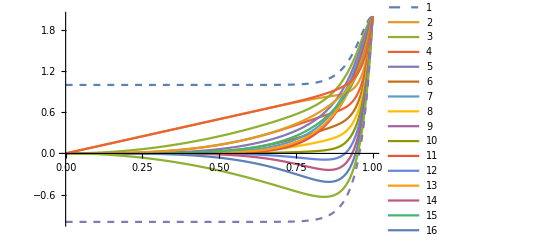

```mathematica
Plot[Evaluate@With[{k=10},Table[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)),{L,2,2k+1}]],{y,0,1},PlotLegends->Automatic,PlotStyle->Flatten@{Dashed,Table[Null,{18}],Dashed}]
```

```mathematica
y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))/.L->j//TeXForm
```

(-1)^j y^{-j+2 k+1}+y^{j+2 k-1}+(-1)^{j-1} y^{-j+4 k+2}+y^{j-2}

### Conjecture: – the pointwise largest poly on (0,1) is the one corresponding to L=2 – the pointwise smallest poly on (0,1) is the one corresponding to L=2k+1. We don’t actually need to prove this. Some weaker properties will suffice, see below.

```mathematica
y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))/.L->2
```

1-y^(4 k)+y^(-1+2 k)+y^(1+2 k)

```mathematica
Simplify[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))/.L->2k+1,k∈Integers]
```

-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k)

### Odd values of L: they are not positive, but pointwise in y monotone decreasing in L (in general they are not pointwise monotone in y for fixed L)

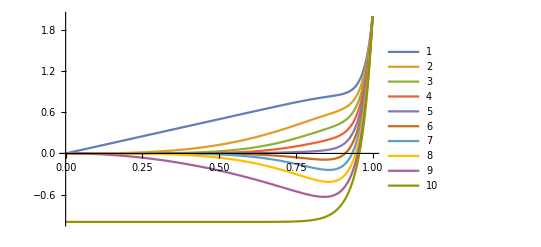

```mathematica
Plot[Evaluate@With[{k=10},Table[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)),{L,3,2k+1,2}]],{y,0,1},PlotRange->All,PlotLegends->Automatic]
```

Here we have  3≤L:=2N+1≤2k+1

```mathematica
(y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))/.L->L+2)-(y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)))//Factor
```

```mathematica
(-1+y) y^(-2-L) (1+y) ((-1)^(1+L) y^(1+2 k)+(-1)^L y^(2+4 k)+y^(2 L)+y^(1+2 k+2 L))
```

(-1+y) y^(-2-L) (1+y) ((-1)^(1+L) y^(1+2 k)+(-1)^L y^(2+4 k)+y^(2 L)+y^(1+2 k+2 L))

```mathematica
((-1)^(1+L) y^(1+2 k)+(-1)^L y^(2+4 k)+y^(2 L)+y^(1+2 k+2 L))/.L->2N+1
```

```mathematica
Simplify[(-1)^(2+2 N) y^(1+2 k)+(-1)^(1+2 N) y^(2+4 k)+y^(2 (1+2 N))+y^(1+2 k+2 (1+2 N)),N∈Integers]
```

y^(1+2 k)-y^(2+4 k)+y^(2+4 N)+y^(3+2 k+4 N)

```mathematica
y^(1+2 k)-y^(2+4 k)//Factor
```

```mathematica
y^(1+2 k) (1-y^(1+2 k))>0
```

### Even values of L: pointwise in y they are not monotone in L, but positive for y∈(0,1)

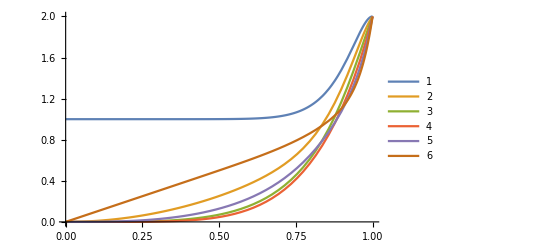

```mathematica
Plot[Evaluate@With[{k=6},Table[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)),{L,2,2k,2}]],{y,0,1},PlotRange->All,PlotLegends->Automatic]
```

Here we have  2≤L:=2N≤2k

```mathematica
Simplify[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))/.L->2N,N∈Integers]
```

y^(-2 (1+N)) (y^(3+2 k)-y^(4+4 k)+y^(4 N)+y^(1+2 k+4 N))

and here

```mathematica
y^(3+2 k)-y^(4+4 k)≥0//Factor
```

```mathematica
y^(3+2 k) (1-y^(1+2 k))≥0
```

### Remark. These y-polys themselves satify a 2nd-order recursion:

```mathematica
Table[Table[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)),{L,2,2k+1}],{k,1,10}]
```

{{1+y+y^3-y^4,-1+y+y^3+y^4},{1+y^3+y^5-y^8,y-y^2+y^6+y^7,y+y^2-y^6+y^7,-1+y^3+y^5+y^8},{1+y^5+y^7-y^12,y-y^4+y^8+y^11,y^2+y^3+y^9-y^10,-y^2+y^3+y^9+y^10,y+y^4-y^8+y^11,-1+y^5+y^7+y^12},{1+y^7+y^9-y^16,y-y^6+y^10+y^15,y^2+y^5+y^11-y^14,y^3-y^4+y^12+y^13,y^3+y^4-y^12+y^13,-y^2+y^5+y^11+y^14,y+y^6-y^10+y^15,-1+y^7+y^9+y^16},{1+y^9+y^11-y^20,y-y^8+y^12+y^19,y^2+y^7+y^13-y^18,y^3-y^6+y^14+y^17,y^4+y^5+y^15-y^16,-y^4+y^5+y^15+y^16,y^3+y^6-y^14+y^17,-y^2+y^7+y^13+y^18,y+y^8-y^12+y^19,-1+y^9+y^11+y^20},{1+y^11+y^13-y^24,y-y^10+y^14+y^23,y^2+y^9+y^15-y^22,y^3-y^8+y^16+y^21,y^4+y^7+y^17-y^20,y^5-y^6+y^18+y^19,y^5+y^6-y^18+y^19,-y^4+y^7+y^17+y^20,y^3+y^8-y^16+y^21,-y^2+y^9+y^15+y^22,y+y^10-y^14+y^23,-1+y^11+y^13+y^24},{1+y^13+y^15-y^28,y-y^12+y^16+y^27,y^2+y^11+y^17-y^26,y^3-y^10+y^18+y^25,y^4+y^9+y^19-y^24,y^5-y^8+y^20+y^23,y^6+y^7+y^21-y^22,-y^6+y^7+y^21+y^22,y^5+y^8-y^20+y^23,-y^4+y^9+y^19+y^24,y^3+y^10-y^18+y^25,-y^2+y^11+y^17+y^26,y+y^12-y^16+y^27,-1+y^13+y^15+y^28},{1+y^15+y^17-y^32,y-y^14+y^18+y^31,y^2+y^13+y^19-y^30,y^3-y^12+y^20+y^29,y^4+y^11+y^21-y^28,y^5-y^10+y^22+y^27,y^6+y^9+y^23-y^26,y^7-y^8+y^24+y^25,y^7+y^8-y^24+y^25,-y^6+y^9+y^23+y^26,y^5+y^10-y^22+y^27,-y^4+y^11+y^21+y^28,y^3+y^12-y^20+y^29,-y^2+y^13+y^19+y^30,y+y^14-y^18+y^31,-1+y^15+y^17+y^32},{1+y^17+y^19-y^36,y-y^16+y^20+y^35,y^2+y^15+y^21-y^34,y^3-y^14+y^22+y^33,y^4+y^13+y^23-y^32,y^5-y^12+y^24+y^31,y^6+y^11+y^25-y^30,y^7-y^10+y^26+y^29,y^8+y^9+y^27-y^28,-y^8+y^9+y^27+y^28,y^7+y^10-y^26+y^29,-y^6+y^11+y^25+y^30,y^5+y^12-y^24+y^31,-y^4+y^13+y^23+y^32,y^3+y^14-y^22+y^33,-y^2+y^15+y^21+y^34,y+y^16-y^20+y^35,-1+y^17+y^19+y^36},{1+y^19+y^21-y^40,y-y^18+y^22+y^39,y^2+y^17+y^23-y^38,y^3-y^16+y^24+y^37,y^4+y^15+y^25-y^36,y^5-y^14+y^26+y^35,y^6+y^13+y^27-y^34,y^7-y^12+y^28+y^33,y^8+y^11+y^29-y^32,y^9-y^10+y^30+y^31,y^9+y^10-y^30+y^31,-y^8+y^11+y^29+y^32,y^7+y^12-y^28+y^33,-y^6+y^13+y^27+y^34,y^5+y^14-y^26+y^35,-y^4+y^15+y^25+y^36,y^3+y^16-y^24+y^37,-y^2+y^17+y^23+y^38,y+y^18-y^22+y^39,-1+y^19+y^21+y^40}}

```mathematica
Table[FindLinearRecurrence[Table[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)),{L,2,2k+1}]],{k,1,10}]
```

{{(-1+y+y^3+y^4)/(1+y+y^3-y^4)},FindLinearRecurrence[{1+y^3+y^5-y^8,y-y^2+y^6+y^7,y+y^2-y^6+y^7,-1+y^3+y^5+y^8}],{(-1+y^2)/y,1},{(-1+y^2)/y,1},{(-1+y^2)/y,1},{(-1+y^2)/y,1},{(-1+y^2)/y,1},{(-1+y^2)/y,1},{(-1+y^2)/y,1},{(-1+y^2)/y,1}}

```mathematica
Expand@RecurrenceTable[{poly[pos+2]==(y^2-1)/y poly[pos+1]+poly[pos],poly[1]==1+y^3+y^5-y^8,poly[2]==y-y^2+y^6+y^7},poly[pos],{pos,1,4}]=={1+y^3+y^5-y^8,y-y^2+y^6+y^7,y+y^2-y^6+y^7,-1+y^3+y^5+y^8}
```

True

```mathematica
Expand@RecurrenceTable[{poly[pos+2]==(y^2-1)/y poly[pos+1]+poly[pos],poly[1]==1+y^5+y^7-y^12,poly[2]==y-y^4+y^8+y^11},poly[pos],{pos,1,6}]=={1+y^5+y^7-y^12,y-y^4+y^8+y^11,y^2+y^3+y^9-y^10,-y^2+y^3+y^9+y^10,y+y^4-y^8+y^11,-1+y^5+y^7+y^12}
```

True

```mathematica
Table[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)),{L,2,3}]
```

{1-y^(4 k)+y^(-1+2 k)+y^(1+2 k),y-y^(-2+2 k)+y^(2+2 k)+y^(-1+4 k)}

```mathematica
RSolve[{poly[pos+2]==(y^2-1)/y poly[pos+1]+poly[pos]},poly[pos],pos]
```

{{poly[pos]→(-1/y)^pos C[1]+y^pos C[2]}}

```mathematica
RSolve[{poly[pos+2]==(y^2-1)/y poly[pos+1]+poly[pos],poly[2]==1-y^(4 k)+y^(-1+2 k)+y^(1+2 k),poly[3]==y-y^(-2+2 k)+y^(2+2 k)+y^(-1+4 k)},poly[pos],pos]
```

{{poly[pos]→-(-(-1/y)^pos y^(3+2 k)+(-1/y)^pos y^(4+4 k)-y^pos-y^(1+2 k+pos))/y^2}}

```mathematica
Simplify[-(-(-1/y)^pos y^(3+2 k)+(-1/y)^pos y^(4+4 k)-y^pos-y^(1+2 k+pos))/y^2,pos∈Integers]
```

```mathematica
(-1)^pos y^(1+2 k-pos)+(-1)^(1+pos) y^(2+4 k-pos)+y^(-2+pos)+y^(-1+2 k+pos)/.pos->L
```

```mathematica
(-1)^L y^(1+2 k-L)+(-1)^(1+L) y^(2+4 k-L)+y^(-2+L)+y^(-1+2 k+L)==y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))//Simplify
```

True

```mathematica
poly[L+2]==(y-1/y)poly[L+1]+poly[L]
```

```mathematica
Factor[λ^2-(y-1/y)λ-1]
```

-((y-λ) (1+y λ))/y

### Conclusion: for odd m=2k+1, the non-negativity of all matrix entries is governed by the interplay between element_(1,1) (leftmost) and element_(1,m) (rightmost). Recall: y==(√(1+(θ ν)^2)-1)/(θ ν), ν>0, 0<θ≤1. And: ν==(2y)/(1-y^2)1/θ, 0<y<1, 0<θ≤1. Mention the terminology: lacunary polynomial / sparse poly / fewnomial (i.e. number of terms fixed while the degree increases)

```mathematica
y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ//TeXForm
```

\theta -(\theta -2) y^{4 k+2}-\theta  y^{4 k+4}+(\theta -2) y^2

```mathematica
Simplify[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2))/.L->2k+1,k∈Integers]
```

```mathematica
-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k)//TeXForm
```

y^{4 k}+y^{2 k-1}+y^{2 k+1}-1

```mathematica
Manipulate[Plot[{y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ,-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k)},{y,0,1}],{θ,0,1},{k,1,20,1}]
```

The yellow curve has been analyzed earlier (see: the θ=1 case). We have now the same situation: 
strictly increasing in y for fixed k, decreasing in k for fixed y, and having a unique root y_R(k)∈(0,1), with asymptotic bounds on y_R(k). Here R stands for right.
(But: in the earlier case we did not have θ-dependence in y.)
Because the yellow curve is -1 at y=0, and 2 at y=1, the above imply that y_R(k) strictly increases when k is increased. We need to recall that lim_(k→∞) y_R(k)=1 from below. This should follow from the asymptotic bound.
And: the yellow curve is <0 on (0,y_R(k)) and positive on (y_R(k),1).
Let us define ν_R(k,θ):=(2y_R(k))/(1-(y_R(k))^2)1/θ∈(0,+∞), for k∈ℕ^+ and any 0<θ≤1.
Hence the top right matrix element is ≥0, if ν≥ν_R(k,θ).

Claim: fix 0<θ≤1 and  k∈ℕ^+. If (2 k)/(1 + 2 k)≤θ≤1, then blue poly>0 for any 0<y<1, so only the yellow poly determines the sign.
If 0<θ<(2 k)/(1 + 2 k), then the blue poly has exactly one root in (0,1), denoted by y_L(k,θ)∈(0,1), and the blue poly is positive on (0,y_L(k,θ)) and negative on (y_L(k,θ),1). Here the subscript L stands for left (entry of the matrix).
Let us define ν_L(k,θ):=(2y_L(k,θ))/(1-(y_L(k,θ))^2)1/θ, for k∈ℕ^+ and any 0<θ<(2 k)/(1 + 2 k).
We extend this definition by ν_L(k,θ):=+∞, for k∈ℕ^+ and any (2 k)/(1 + 2 k)≤θ≤1.
Hence the top left matrix element is ≥0, if ν≤ν_L(k,θ).
We know from above that the full matrix is non-negative if both the top left and the top right elements are non-negative.

Hence for k∈ℕ^+ and any 0<θ≤1, the matrix is non-negative iff  ν_R(k,θ)≤ν≤ν_L(k,θ).

Claim:  for k∈ℕ^+ and any 0<θ<1/2, ν_R(k,θ)>ν_L(k,θ), so the matrix cannot be non-negative.

For θ=1 the statement is clear:

```mathematica
y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->1//Factor
```

```mathematica
(1-y^2) (1+y^(2+4 k))
```

For 0<θ<1: the blue poly has a root in (0,1) iff θ==(2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k))). The case of inequalities is similar; the blue poly is = θ at y=0, and = 0 at y=1. FIGURE of a TYPICAL BLUE and YELLOW POLY.

```mathematica
y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ//Expand
```

```mathematica
θ(1+y^2) (1-y^(2+4 k))-2 y^2 (1-y^(4 k))
```

```mathematica
Solve[y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ==0,θ]
```

```mathematica
{{θ->(2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k)))}}
```

Here (2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k))) at y=0 is 0, and lim_(y→1-) (2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k)))=(2 k)/(1+2 k),

```mathematica
Limit[(2 y^2 (-1+y^(4 k)))/((1+y^2) (-1+y^(2+4 k))),y->1]
```

(2 k)/(1+2 k)

and for fixed k, (2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k))) is strictly increasing:

```mathematica
D[(2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k))),y]//Simplify
```

-(4 y (-1+(1+2 k) y^(4 k)-(1+2 k) y^(4+4 k)+y^(4+8 k)))/((1+y^2)^2 (-1+y^(2+4 k))^2)

```mathematica
-(-1+(1+2 k) y^(4 k)-(1+2 k) y^(4+4 k)+y^(4+8 k))//Expand//Simplify
```

1-(1+2 k) y^(4 k)+(1+2 k) y^(4+4 k)-y^(4+8 k)

Since the above poly is 1 at y=0, and 0 at y=1, for its positivity it is enough to show that 1-(1+2 k) y^(4 k)+(1+2 k) y^(4+4 k)-y^(4+8 k) is strictly decreasing in y:

```mathematica
D[1-(1+2 k) y^(4 k)+(1+2 k) y^(4+4 k)-y^(4+8 k),y]//Simplify
```

-4 (1+2 k) y^(-1+4 k) (k-k y^4+y^4 (-1+y^(4 k)))

So it is enough to show that k-k y^4+y^4 (-1+y^(4 k))>0 for 0<y<1. But

```mathematica
k-k y^4+y^4 (-1+y^(4 k))/.y->0
```

```mathematica
Simplify[0 (-1+0^(4 k))+k,k>0]
```

k

```mathematica
k-k y^4+y^4 (-1+y^(4 k))/.y->1
```

0

```mathematica
D[k-k y^4+y^4 (-1+y^(4 k)),y]//Simplify
```

4 (1+k) y^3 (-1+y^(4 k))

Q.E.D.

```mathematica
Manipulate[Plot[{(2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k))),8/9},{y,0,1},PlotRange->{0,1}],{k,1,20,1}]
```

General::munfl: (2.04082×10^-8)^62 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.04082×10^-8)^46 is too small to represent as a normalized machine number; precision may be lost.

Question. Fix 0<θ<1 and  k∈ℕ^+ such that 0<θ<(2 k)/(1 + 2 k). (Then the blue poly has exactly one root in (0,1), denoted by y_L(k,θ)∈(0,1), and it is positive on (0,y_L(k,θ)) and negative on (y_L(k,θ),1).)
What happens to y_L(k,θ) when k is increased? Remark: since (2 k)/(1 + 2 k) is increasing in k, the condition 0<θ<(2 k)/(1 + 2 k) is not violated when k is increased.
Answer:  for fixed 0<y<1, (2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k)))is strictly increasing in k. Hence y_L(k,θ) strictly decreases when k is increased: see the slicing property above.
Proof:

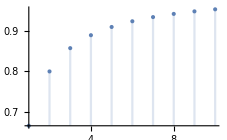

```mathematica
DiscretePlot[(2k)/(2k+1),{k,1,10}]
```

```mathematica
((2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k)))/.k->k+1)-(2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k)))//Simplify
```

(2 y^(2+4 k) (-1+y^2)^2)/((-1+y^(2+4 k)) (-1+y^(6+4 k)))

Q.E.D.

Question. What happens to y_L(k,θ) when k∈ℕ^+ is kept fixed, and θ  is changed in the interval (0,(2 k)/(1 + 2 k))? 
Answer:  for fixed k∈ℕ^+ and θ∈(0,(2 k)/(1 + 2 k)),  y_L(k,θ) is defined as the unique solution y of the equation  θ==(2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k))). The RHS is strictly increasing in y, and the LHS is a constant line. If the LHS is increased, the intersection point moves to the right. Hence y_L(k,θ) strictly increases when θ is increased. Q.E.D.

Claim: ∃lim_(θ→(2 k)/(1 + 2 k)-0) y_L(k,θ)=1, from below. 
Claim: ∃lim_(θ→0+) y_L(k,θ)=0, from above. 

This follows from the limit properties of the function (2 y^2 (1-y^(4 k)))/((1+y^2) (1-y^(2+4 k))).
The above mean if θ→(2 k)/(1 + 2 k)-0, then ν_L(k,θ) → +∞,  due to the relation  y==(√(1+(θ ν)^2)-1)/(θ ν) .
And if θ→0+0, then ν_L(k,θ) → 0.

```mathematica
Manipulate[Plot[{y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ,-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k)},{y,0,1}],{θ,0,(2k)/(2k+1)},{k,1,20,1}]
```

### Claim: for fixed 0<θ<1, ∃lim_(k→∞) y_L(k,θ)=√(θ/(2-θ))∈(0,1). Proof: y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ==0 and here the limit is y^2 (-2+θ)+θ==0. In other words: lim_(k→+∞) ν_L(k,θ)==1/(1-θ)√(2/θ-1). NB. There is no conflict with our earlier definition: ν_L(k,θ):=+∞, for k∈ℕ^+ and any (2 k)/(1 + 2 k)≤θ≤1. On the other hand, from the asymptotic bound we have that for fixed 0<θ≤1, ∃lim_(k→∞) ν_R(k,θ)=+∞. By “for k∈ℕ^+ and any 0<θ≤1, the matrix is non-negative iff 0<ν_R(k,θ)≤ν≤ν_L(k,θ)≤+∞" we have that for any fixed 0<θ<1, the matrix can be non-negative only for a finite set of k values. On the plots: the blue regions shift to the right as k is increased.

```mathematica
Reduce[√(θ/(2-θ))==(-1+√(1+θ^2 ν^2))/(θ ν)&&0<θ≤1&&ν>0,ν]//Simplify
```

```mathematica
0<θ<1&&1/(1-θ)√(2/θ-1)==ν
```

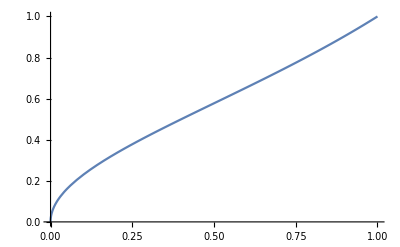

```mathematica
Plot[√(θ/(2-θ)),{θ,0,1}]
```

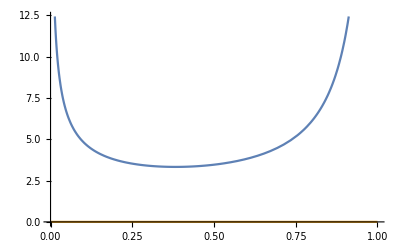

```mathematica
Plot[{1/(1-θ)√(2/θ-1),0},{θ,0,1}]
```

```mathematica
D[1/(1-θ)√(2/θ-1),θ]==0//Solve
```

```mathematica
{{θ->1/2 (3-√5)},{θ->1/2 (3+√5)}}//N
```

{{θ→0.381966},{θ→2.61803}}

```mathematica
Manipulate[FindRoot[(2 y^2 (-1+y^(4 k)))/((1+y^2) (-1+y^(2+4 k)))==1/3,{y,0.5},WorkingPrecision->29],{k,1,20,1}]
```

```mathematica
Manipulate[RootReduce@Reduce[(2 y^2 (-1+y^(4 k)))/((1+y^2) (-1+y^(2+4 k)))==1/3&&0<y<1,y,Reals],{k,1,20,1}]
```

Theorem. Suppose in the following that θ∈[0,1], ν>0, k∈ℕ^+, m=2k+1,  and  M(θ,ν,m):=(I-θ ν L)^-1(I+(1-θ)ν L) is the full dicretization matrix of size m x m. It is circulant. 

Fix an arbitrary 0≤θ<1/2. Then  M(θ,ν,m)≥0 can never hold, i.e. for any ν>0 and  m=2k+1, there is at least one strictly negative entry of M(θ,ν,m).

Let θ:=1/2. Then  M(1/2,ν,3)≥0 ⧦ ν=4. For k≥2,  M(1/2,ν,2k+1)≥0 can never hold, i.e. for any ν>0 and  m=2k+1≥5, there is at least one strictly negative entry of M(θ,ν,m).

Fix any  1/2<θ<1. Then there are finitely many values of k for which ...

Fix θ=1. Then ...

Date when writing this part: 2020. 02. 02.

The formula to reconstruct ν from y:

```mathematica
Reduce[y==(-1+√(1+θ^2 ν^2))/(θ ν)&&0<y<1&&0<θ≤1&&ν>0,ν]//Simplify
```

```mathematica
0<θ≤1&&0<y<1&&ν==2/θ y/(1-y^2)
```

```mathematica
Reduce[y==(-1+√(1+θ^2 ν^2))/(θ ν)&&0<y<1&&0<θ≤1&&ν>0,θ]//Simplify
```

```mathematica
ν>0&&y>0&&√(1+1/ν^2)≥y+1/ν&&θ==(2 y)/(ν(1-y^2 ))
```

### Remark: The matrix corresponding to M(1/2,4,3) is the following. It is a corner point.

```mathematica
With[{k=1,θ=1/2},Reduce[y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ==-1+y^(2 k) (1/y+y+y^(2 k))&&y>0,y,Reals]]
```

y==1/2 (-1+√5)

```mathematica
1/2 (-1+√5)==(-1+√(1+θ^2 ν^2))/(θ ν)/.θ->1/2//Solve
```

{{ν→4}}

```mathematica
With[{θ=1/2},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))//Simplify//Expand,{m,3,3,2}]]/.ν->4
```

{(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)}

```mathematica
With[{θ=4/5},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))//Simplify//Expand,{m,5,5,2}]]
```

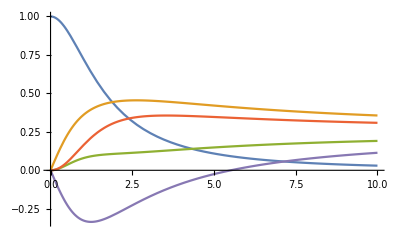

```mathematica
Plot[Evaluate@{({{(25 (5+2 ν^2))/(125+100 ν^2+16 ν^4), (ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4)}, {(ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (25 (5+2 ν^2))/(125+100 ν^2+16 ν^4), (ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4)}, {(ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (25 (5+2 ν^2))/(125+100 ν^2+16 ν^4), (ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4)}, {(ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (25 (5+2 ν^2))/(125+100 ν^2+16 ν^4), (ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4)}, {(ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (25 (5+2 ν^2))/(125+100 ν^2+16 ν^4)}})}[[1,1]],{ν,0,10}]
```

```mathematica
Reduce[And@@Thread[Evaluate@{({{(25 (5+2 ν^2))/(125+100 ν^2+16 ν^4), (ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4)}, {(ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (25 (5+2 ν^2))/(125+100 ν^2+16 ν^4), (ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4)}, {(ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (25 (5+2 ν^2))/(125+100 ν^2+16 ν^4), (ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4)}, {(ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (25 (5+2 ν^2))/(125+100 ν^2+16 ν^4), (ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4)}, {(ν (125+40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (ν^2 (25-10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν^2 (25+10 ν+4 ν^2))/(125+100 ν^2+16 ν^4), (ν (-125-40 ν^2+8 ν^3))/(250+200 ν^2+32 ν^4), (25 (5+2 ν^2))/(125+100 ν^2+16 ν^4)}})}[[1,1]]≥0]&&ν>0]
```

```mathematica
ν≥Root[-125-40 #1^2+8 #1^3&,1]//N
```

ν≥5.51392

```mathematica
Reduce[(-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k)==0/.k->2)&&0<y<1]
```

y==Root[-1+#1^2+#1^3-#1^4+#1^6&,2]

```mathematica
ν==2/θ y/(1-y^2)/.y->Root[-1+#1^2+#1^3-#1^4+#1^6&,2]/.θ->4/5//RootReduce
```

ν==Root[-125-40 #1^2+8 #1^3&,1]

It seems easier to describe the non-negativity set for fixed k∈ℕ^+, that is, the set {(θ,ν)∈[0,1] x (0,+∞):  M(θ, ⋁, 2 k + 1) ≥0}.
The bottom curve has the equation ν==(2y^*(k))/(1-(y^*(k))^2)1/θ, a hyperbola.
The vertical asymptote for the steep left edge has equation θ=(m-1)/m=(2k)/(2k+1).
For any k and θ∈[0,1/2), the non-negativity set is empty.
The θ-coordinate of the corner point satisfies the following: the unique root of the blue poly coincides with the unique root of the yellow poly. Why do we have such a coinciding point?
What are the matrices corresponding to the “corner” parameter values for k=2, k=3, k=4? Those are the ones when topleft=0=topright. The row sums are 1.

```mathematica
Solve[y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ==0/.k->2]
```

{{y→-1},{y→-ⅈ},{y→ⅈ},{y→1},{θ→(2 (y^2+y^6))/(1+y^2+y^4+y^6+y^8)}}

```mathematica
-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k)==0/.k->2
```

-1+y^3+y^5+y^8==0

```mathematica
Reduce[-1+y^3+y^5+y^8==0&&0<y<1]
```

y==Root[-1+#1^2+#1^3-#1^4+#1^6&,2]

```mathematica
y==-ⅈ||y==ⅈ||y==Root[-1+#1^2+#1^3-#1^4+#1^6&,1]||y==Root[-1+#1^2+#1^3-#1^4+#1^6&,2]||y==Root[-1+#1^2+#1^3-#1^4+#1^6&,3]||y==Root[-1+#1^2+#1^3-#1^4+#1^6&,4]||y==Root[-1+#1^2+#1^3-#1^4+#1^6&,5]||y==Root[-1+#1^2+#1^3-#1^4+#1^6&,6]//N
```

y==0.-1. ⅈ||y==0.+1. ⅈ||y==-1.25207||y==0.798675||y==-0.585556-0.614838 ⅈ||y==-0.585556+0.614838 ⅈ||y==0.812255-0.852873 ⅈ||y==0.812255+0.852873 ⅈ

```mathematica
(-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k))/(1+y^2)//Simplify
```

(-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k))/(1+y^2)

```mathematica
θ->(2 (y^2+y^6))/(1+y^2+y^4+y^6+y^8)/.y->Root[-1+#1^2+#1^3-#1^4+#1^6&,2]//RootReduce
```

θ→Root[-2+5 #1-6 #1^2+4 #1^3&,1]

```mathematica
θ->Root[-2+5 #1-6 #1^2+4 #1^3&,1]//N[#,16]&
```

θ→0.7266988257582019

```mathematica
y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ==0/.k->2
```

y^2 (-2+θ)-y^10 (-2+θ)+θ-y^12 θ==0

```mathematica
(y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ)/((1+y^2)(1-y^2))//Simplify
```

(-y^2 (-2+θ)+y^(2+4 k) (-2+θ)-θ+y^(4+4 k) θ)/(-1+y^4)

```mathematica
y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ==0/.k->2/.θ->Root[-2+5 #1-6 #1^2+4 #1^3&,1]
```

y^2 (-2+Root[-2+5 #1-6 #1^2+4 #1^3&,1])-y^10 (-2+Root[-2+5 #1-6 #1^2+4 #1^3&,1])+Root[-2+5 #1-6 #1^2+4 #1^3&,1]-y^12 Root[-2+5 #1-6 #1^2+4 #1^3&,1]==0

```mathematica
Reduce[y^2 (-2+Root[-2+5 #1-6 #1^2+4 #1^3&,1])-y^10 (-2+Root[-2+5 #1-6 #1^2+4 #1^3&,1])+Root[-2+5 #1-6 #1^2+4 #1^3&,1]-y^12 Root[-2+5 #1-6 #1^2+4 #1^3&,1]==0&&-1+y^3+y^5+y^8==0&&0<y<1]//RootReduce
```

```mathematica
y==Root[-1+#1^2+#1^3-#1^4+#1^6&,2]//N
```

y==0.798675

```mathematica
ν==(2 SuperStar[y](k))/(1-(SuperStar[y](k))^2)1/θ
```

```mathematica
ν==(2 SuperStar[y][k])/(θ (1-(SuperStar[y][k])^2))/.SuperStar[y][k]->Root[-1+#1^2+#1^3-#1^4+#1^6&,2]/.θ->Root[-2+5 #1-6 #1^2+4 #1^3&,1]//RootReduce
```

```mathematica
ν==Root[-16-16 #1-3 #1^2+#1^3&,1]//N
```

ν==6.07011

```mathematica
With[{θ=θ},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))//Simplify//Expand,{m,5,5,2}]]
```

```mathematica
({{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}, {(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4), (16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4)}})/.ν->Root[-16-16 #1-3 #1^2+#1^3&,1]/.θ->Root[-2+5 #1-6 #1^2+4 #1^3&,1]//RootReduce//MatrixForm
```

```mathematica
({{0, Root[-1+2 #1+#1^3&,1], Root[-1+7 #1-7 #1^2+2 #1^3&,1], Root[-1+2 #1+#1^2+2 #1^3&,1], 0}, {0, 0, Root[-1+2 #1+#1^3&,1], Root[-1+7 #1-7 #1^2+2 #1^3&,1], Root[-1+2 #1+#1^2+2 #1^3&,1]}, {Root[-1+2 #1+#1^2+2 #1^3&,1], 0, 0, Root[-1+2 #1+#1^3&,1], Root[-1+7 #1-7 #1^2+2 #1^3&,1]}, {Root[-1+7 #1-7 #1^2+2 #1^3&,1], Root[-1+2 #1+#1^2+2 #1^3&,1], 0, 0, Root[-1+2 #1+#1^3&,1]}, {Root[-1+2 #1+#1^3&,1], Root[-1+7 #1-7 #1^2+2 #1^3&,1], Root[-1+2 #1+#1^2+2 #1^3&,1], 0, 0}})//N//MatrixForm
```

```mathematica
({{0., 0.45339765151640377, 0.17051645904150295, 0.37608588944209326, 0.}, {0., 0., 0.45339765151640377, 0.17051645904150295, 0.37608588944209326}, {0.37608588944209326, 0., 0., 0.45339765151640377, 0.17051645904150295}, {0.17051645904150295, 0.37608588944209326, 0., 0., 0.45339765151640377}, {0.45339765151640377, 0.17051645904150295, 0.37608588944209326, 0., 0.}})[[1]]
```

```mathematica
{0.,0.45339765151640377,0.17051645904150295,0.37608588944209326,0.}//Total
```

1.

```mathematica
Reduce[16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4==0&&ν (-8-4 θ^2 ν^2+θ^3 ν^3)==0,Reals,Backsubstitution->True]//RootReduce
```

```mathematica
ν==Root[-16-16 #1-3 #1^2+#1^3&,1]&&θ==Root[-2+5 #1-6 #1^2+4 #1^3&,1]//N
```

ν==6.07011&&θ==0.726699

### For figures

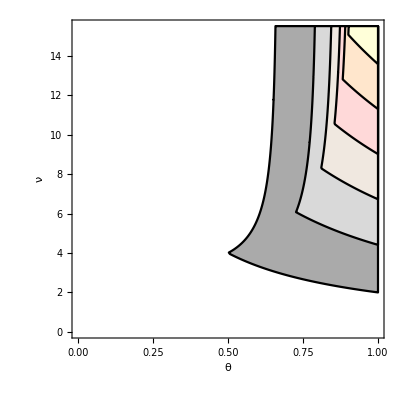

```mathematica
Show@Table[RegionPlot[Evaluate[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,15.5},PlotPoints->80,PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]},BoundaryStyle->Black,FrameLabel->{θ,ν},RotateLabel->False],{m,3,13,2}]
```

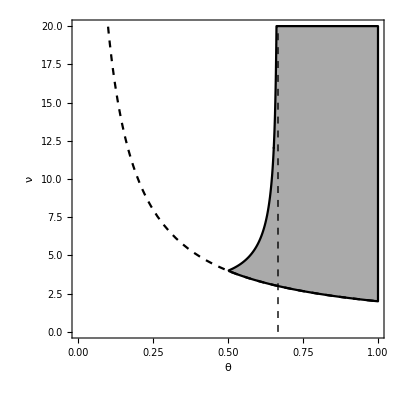

```mathematica
With[{m=3},Show[RegionPlot[Evaluate[A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;LogicalExpand@Reduce[(0≤θ≤1)&&(ν≥0)&&And@@Thread[Union@Flatten[Simplify[Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A)]]≥0],θ]],{θ,0,1},{ν,0,20},PlotPoints->60,BoundaryStyle->Black,PlotStyle->{Lighter@Gray},FrameLabel->{θ,ν},RotateLabel->False],Graphics[{Dashed,Line[{{(m-1)/m,0},{(m-1)/m,20}}]}],Plot[{2/θ},{θ,0,1},PlotStyle->{Black,Dashed}]]]
```

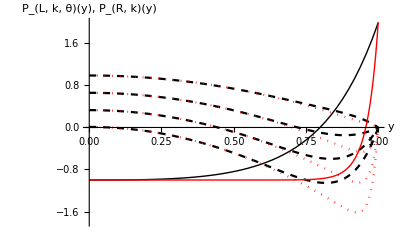

```mathematica
Show[With[{k=2},Plot[Evaluate[{y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->0.01,y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->0.33,y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->0.66,y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->0.99,-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k)}],{y,0,1},PlotRange->{-1.8,2},PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Thick}},AxesLabel->{y,"P_(L, k, θ)(y), P_(R, k)(y)"}]],With[{k=10},Plot[Evaluate[{y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->0.01,y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->0.33,y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->0.66,y^2 (-2+θ)-y^(2+4 k) (-2+θ)+θ-y^(4+4 k) θ/.θ->0.99,-1+y^(4 k)+y^(-1+2 k)+y^(1+2 k)}],{y,0,1},PlotRange->{-1.8,2},PlotStyle->{{Red,Dotted},{Red,Dotted},{Red,Dotted},{Red,Dotted},{Red,Thick}}]]]
```

### We plot those polynomials appearing in the first row, starting from position 2, which determine the sign of the matrix

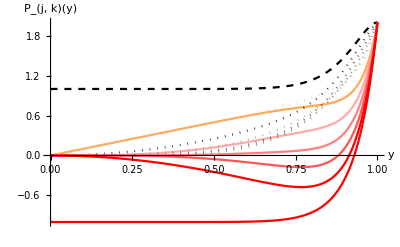

```mathematica
Plot[Evaluate@With[{k=6},Table[y^(L-2)+(-1)^L y^(2 k-(L-1))+y^(2 k+L-1)+(-1)^(L-1)y^(4 k-(L-2)),{L,2,2k+1}]],{y,0,1},PlotStyle->Join[{{Dashed,Thickness[.004],Black}},Riffle[{{RGBColor[1, 0.6666666666666666, Rational[1, 3]]},{RGBColor[1, 0.6666666666666666, 0.6666666666666666]},{RGBColor[1, 0.5, 0.5]},{RGBColor[1, Rational[1, 3], Rational[1, 3]]},{RGBColor[1, 0, 0]}},Table[{GrayLevel[α],Dotted},{α,0,0.8,0.2}]],{{Red,Thickness[.004]}}],AxesLabel->{y,"P_(j, k)(y)"}]
```

```mathematica
Join[{{Dashed,Thickness[.004],Black}},Riffle[{{RGBColor[1, 0.6666666666666666, Rational[1, 3]]},{RGBColor[1, 0.6666666666666666, 0.6666666666666666]},{RGBColor[1, 0.5, 0.5]},{RGBColor[1, Rational[1, 3], Rational[1, 3]]},{RGBColor[1, 0, 0]}},Table[{GrayLevel[α],Dotted},{α,0,0.8,0.2}]],{{Red,Thickness[.004]}}]
```

{{Dashing[{Small,Small}],Thickness[0.004],GrayLevel[0]},{RGBColor[1, 0.6666666666666666, Rational[1, 3]]},{GrayLevel[0.],Dashing[{0,Small}]},{RGBColor[1, 0.6666666666666666, 0.6666666666666666]},{GrayLevel[0.2],Dashing[{0,Small}]},{RGBColor[1, 0.5, 0.5]},{GrayLevel[0.4],Dashing[{0,Small}]},{RGBColor[1, Rational[1, 3], Rational[1, 3]]},{GrayLevel[0.6000000000000001],Dashing[{0,Small}]},{RGBColor[1, 0, 0]},{GrayLevel[0.8],Dashing[{0,Small}]},{RGBColor[1, 0, 0],Thickness[0.004]}}

### Color test

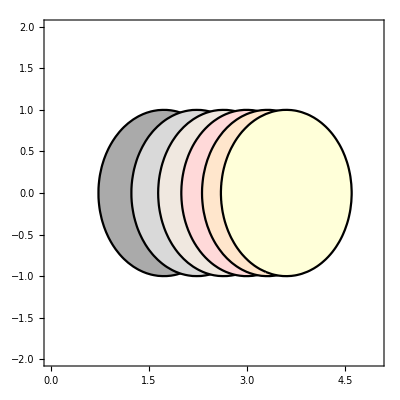

```mathematica
Show@Table[RegionPlot[(x-√m)^2+y^2<1,{x,0,5},{y,-2,2},PlotStyle->{Which[m==3,Lighter@Gray,m==5,LightGray,m==7,LightBrown,m==9,LightRed,m==11,LightOrange,m==13,LightYellow]},BoundaryStyle->Black],{m,3,13,2}]
```